## Diploid VCF: Determining sites with only heterozygous calls

Uploading full diploid VCF

```mathematica
fullgenomeDIP=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/07_genomicsDB/full_genome.vcf"];
```

```mathematica
fullheader=fullgenomeDIP[[1;;58]];
```

```mathematica
header=fullgenomeDIP[[58]];
```

```mathematica
fullgenomeDIP=Drop[fullgenomeDIP,58];
```

```mathematica
header
```

{#CHROM,POS,ID,REF,ALT,QUAL,FILTER,INFO,FORMAT,CdBM23_S1,CdBM25_S10,CdBM26_S18,CdBM29_S26,CdBM30_S34,CdBM32_S42,CdBM36_S50,CdBM37_S58,CdBM39_S2,CdBM42_S11,CdBM43_S19,CdBM44_S27,CdBM45_S35,CdBM46_S43,CdBM47_S51,CdBM48_S59,CoBM12_S4,CoBM14_S13,CoBM15_S21,CoBM16_S29,CoBM17_S37,CoBM18_S45,CoBM1_S3,CoBM20_S53,CoBM21_S61,CoBM2_S12,CoBM3_S20,CoBM4_S28,CoBM5_S36,CoBM6_S44,CoBM7_S52,CoBM8_S60,CuBM10_S54,CuBM11_S62,CuBM12_S6,CuBM13_S15,CuBM14_S23,CuBM15_S31,CuBM16_S39,CuBM17_S47,CuBM18_S55,CuBM3_S5,CuBM4_S14,CuBM6_S22,CuBM7_S30,CuBM8_S38,CuBM9_S46,MnBM12_S63,MnBM13_S7,MnBM14_S16,MnBM15_S24,MnBM16_S32,MnBM17_S40,MnBM18_S48,MnBM20_S56,MnBM21_S64,MnBM23_S8,MnBM24_S17,MnBM25_S25,MnBM27_S33,MnBM28_S41,MnBM29_S49,MnBM31_S57,MnBM32_S65,MnBM34_S66,MnBM38_S72,MnBM39_S78,MnBM42_S84,MnBM44_S90,NiBM11_S73,NiBM12_S79,NiBM14_S85,NiBM16_S91,NiBM17_S97,NiBM21_S103,NiBM22_S109,NiBM24_S68,NiBM25_S74,NiBM27_S80,NiBM28_S86,NiBM29_S92,NiBM30_S98,NiBM4_S96,NiBM6_S102,NiBM8_S108,NiBM9_S67,OLY077_S101,ZnBM11_S104,ZnBM12_S110,ZnBM15_S69,ZnBM16_S75,ZnBM17_S81,ZnBM19_S87,ZnBM22_S93,ZnBM23_S99,ZnBM25_S105,ZnBM28_S111,ZnBM29_S70,ZnBM31_S76,ZnBM34_S82,ZnBM37_S88,ZnBM38_S94,ZnBM39_S100,ZnBM41_S106,ZnBM42_S112,ZnBM43_S71,ZnBM44_S77,ZnBM45_S83,ZnBM46_S89,ZnBM47_S95}

```mathematica
Length[fullgenomeDIP]
```

19627

Keeps only those sites with depth ≥5 and that have some “1|1” calls (stripping out heterozygous only calls):

```mathematica
droppos=-1+Position[header,"CdBM23_S1"][[1,1]];(*# columns to be dropped before first sample*)
```

```mathematica
genomeDIP=Table[".|.",{i,1,Length[fullgenomeDIP]},{j,1,Length[header]-droppos}];
```

```mathematica
For[i=1,i≤Length[fullgenomeDIP],i++,
For[j=1+droppos,j≤Length[header],j++,
temp=StringSplit[fullgenomeDIP[[i,j]],{":"}];
If[temp[[1]]≠".|.",If[Length[temp]≥3,
	If[ToExpression[temp[[3]]]≥5,genomeDIP[[i,j-droppos]]=StringReplace[temp[[1]],"/"->"|"]]]];
(*Strips out difference in phasing information*)
]
]
```

```mathematica
genomeDIP//Length
```

19627

```mathematica
For[i=1;keep=Table[1,{i,1,Length[genomeDIP]}],i≤Length[genomeDIP],i++,
tally=Tally[genomeDIP[[i]]];
If[Length[Position[tally,"1|1"]]==0,keep[[i]]=0]
]
```

```mathematica
keeptable={};
droptableDIP={};
For[i=1,i≤Length[genomeDIP],i++,
If[keep[[i]]>0,
keeptable=AppendTo[keeptable,fullgenomeDIP[[i,1;;2]]],droptableDIP=AppendTo[droptableDIP,fullgenomeDIP[[i,1;;2]]]];
]
```

```mathematica
keeptable[[1;;10]]
```

{{ref|NC_001133|,12690},{ref|NC_001133|,15592},{ref|NC_001133|,19971},{ref|NC_001133|,23712},{ref|NC_001133|,23713},{ref|NC_001133|,25340},{ref|NC_001133|,25487},{ref|NC_001133|,25488},{ref|NC_001133|,25489},{ref|NC_001133|,25497}}

```mathematica
Length[keeptable]
```

11300

```mathematica
Length[droptableDIP]
```

8327

```mathematica
Export["sitestokeep.csv",keeptable];
```

## Looking at data from snpEff

### Uploading data

Converting information from snpEff

```mathematica
fullgenomeSNPEFF=Import["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/snpEff_RMheterozygotes_RMmodifiers_4Nov2024.tsv"];
```

```mathematica
header=fullgenomeSNPEFF[[1]]
```

{CHROM,chr,POS,REF,ALT,QUAL,FORMAT,gene,effect,mut_type,gene_code,base_change,aa_change,ANN,OLY077_S101,CdBM23_S1,CdBM25_S10,CdBM26_S18,CdBM29_S26,CdBM30_S34,CdBM32_S42,CdBM36_S50,CdBM37_S58,CdBM39_S2,CdBM42_S11,CdBM43_S19,CdBM44_S27,CdBM45_S35,CdBM46_S43,CdBM47_S51,CdBM48_S59,CoBM12_S4,CoBM14_S13,CoBM15_S21,CoBM16_S29,CoBM17_S37,CoBM18_S45,CoBM1_S3,CoBM20_S53,CoBM21_S61,CoBM2_S12,CoBM3_S20,CoBM4_S28,CoBM5_S36,CoBM6_S44,CoBM7_S52,CoBM8_S60,CuBM10_S54,CuBM11_S62,CuBM12_S6,CuBM13_S15,CuBM14_S23,CuBM15_S31,CuBM16_S39,CuBM17_S47,CuBM18_S55,CuBM3_S5,CuBM4_S14,CuBM6_S22,CuBM7_S30,CuBM8_S38,CuBM9_S46,MnBM12_S63,MnBM13_S7,MnBM14_S16,MnBM15_S24,MnBM16_S32,MnBM17_S40,MnBM18_S48,MnBM20_S56,MnBM21_S64,MnBM23_S8,MnBM24_S17,MnBM25_S25,MnBM27_S33,MnBM28_S41,MnBM29_S49,MnBM31_S57,MnBM32_S65,MnBM34_S66,MnBM38_S72,MnBM39_S78,MnBM42_S84,MnBM44_S90,NiBM11_S73,NiBM12_S79,NiBM14_S85,NiBM16_S91,NiBM17_S97,NiBM21_S103,NiBM22_S109,NiBM24_S68,NiBM25_S74,NiBM27_S80,NiBM28_S86,NiBM29_S92,NiBM30_S98,NiBM4_S96,NiBM6_S102,NiBM8_S108,NiBM9_S67,ZnBM11_S104,ZnBM12_S110,ZnBM15_S69,ZnBM16_S75,ZnBM17_S81,ZnBM19_S87,ZnBM22_S93,ZnBM23_S99,ZnBM25_S105,ZnBM28_S111,ZnBM29_S70,ZnBM31_S76,ZnBM34_S82,ZnBM37_S88,ZnBM38_S94,ZnBM39_S100,ZnBM41_S106,ZnBM42_S112,ZnBM43_S71,ZnBM44_S77,ZnBM45_S83,ZnBM46_S89,ZnBM47_S95,AC,AF,AN,BaseQRankSum,DP,FS,MLEAC,MLEAF,MQ,MQRankSum,QD,ReadPosRankSum,SOR,LOF}

```mathematica
fullgenomeSNPEFF=Drop[fullgenomeSNPEFF,1];
```

Keeps only those sites with depth ≥5 and that have some “1|1” calls (stripping out heterozygous only calls):

```mathematica
droppos=-1+Position[header,"OLY077_S101"][[1,1]]; (*# columns to be dropped before first sample*)
```

```mathematica
topos=Position[header,"ZnBM47_S95"][[1,1]]; (*# last metal column*)
```

```mathematica
genelist=Sort[Union[fullgenomeSNPEFF[[All,8]]]]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSC1,BSD2,BUD19,BUL1,BUL2,CAJ1,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DAN4,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FLO1,FLO9,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GCD2,GPB1,GPB2,GPH1,GSC2,HAP1,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS11,MSS2,MTR4,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PIR3,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,tC(GCA)B,TCO89,tE(UUC)G3,TFB1,TFG1,TIM54,tK(CUU)E2,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TRT2,tS(AGA)M,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS63,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBL109W,YBR134W,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL176W,YDL199C,YDR003W-A,YDR157W,YDR269C,YDR381C-A,YDR541C,YDR544C,YEF1,YER087C-A,YER156C,YFL021C-A,YFR036W-A,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YHL008C,YHR028W-A,YHR071C-A,YIH1,YIL092W,YIR020W-A,YJL211C,YKR073C,YLL020C,YLL066W-B,YLR108C,YLR296W,YLR312C,YLR372W,YML119W,YMR027W,YMR317W,YNL109W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL025C,YPL114W,YPR078C,YPR089W,YPR117W,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

Plotting the depth of coverage at that site:

```mathematica
Max[fullgenomeSNPEFF[[All,129]]]
```

17792

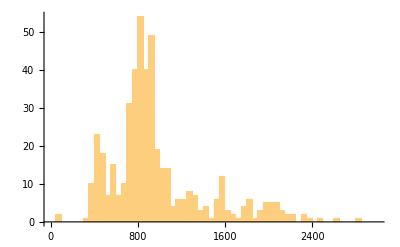

```mathematica
fullgenedepth=Histogram[fullgenomeSNPEFF[[All,129]],{50},PlotRange->{{0,3000},Automatic}]
```

There are two low outliers (BSC1 and HAP1, filtered out below for having too many “.” genotypes):

```mathematica
Select[fullgenomeSNPEFF[[All,129]],#<300&]
```

{91,84}

There are three high outliers (all FLO1, filtered out below for having too many “.” genotypes):

```mathematica
Select[fullgenomeSNPEFF[[All,129]],#>3000&]
```

{15599,15734,17792}

Mean depth:

```mathematica
Mean[fullgenomeSNPEFF[[All,129]]]//N
```

1072.34

### Dropping tRNAs, checking overlapping coding regions (snpEff), and dropping dubious genes

Dropping tRNAs, which we drop {“tC(GCA)B”,”tE(UUC)G3”,”tK(CUU)E2”,”tS(AGA)M”} and TRT2 (which is tT(CGU)K), but first checking that their annotations from snpEff do not involve other genes (other than upstream or downstream modifiers):

```mathematica
dropgenes={"tC(GCA)B","tE(UUC)G3","tK(CUU)E2","tS(AGA)M","TRT2"};
```

Depth of coverage for these genes is pretty typical:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropgenes,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{tC(GCA)B,1316},{tK(CUU)E2,1111},{tE(UUC)G3,398},{TRT2,2091},{tS(AGA)M,885}}

1160.2

Dropping these five tRNAs

```mathematica
Length[fullgenomeSNPEFF];
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,MemberQ[dropgenes,#[[8]]]==False&];
%%-Length[fullgenomeSNPEFF]
```

5

Looking over all genes whose most extreme snpEff calls involve more than one protein-coding gene:

```mathematica
catSNPEFF={"LOW","MODERATE","HIGH"}; (*Not "MODIFIER"*)
```

```mathematica
Clear[sumFULL]
sumFULL=Table["ERROR",{i,1,Length[fullgenomeSNPEFF]}];
For[i=1,i≤Length[fullgenomeSNPEFF],i++,
temp=StringSplit[fullgenomeSNPEFF[[i,14]],{"|"}];
temp2=Tally[temp];
temp3=Select[temp2,MemberQ[catSNPEFF,#[[1]]]&];
sumFULL[[i]]=Total[temp3][[2]]
]
```

```mathematica
Position[sumFULL,_?(#>1&)]
```

{{84},{120},{227},{229},{296},{317},{356},{380},{439}}

```mathematica
Position[sumFULL,_?(#>2&)]
```

{}

#### #84: YDR269C is dubious, but CCC2 is verified (SGD) [Updated]

```mathematica
fixme=84;
```

```mathematica
fullgenomeSNPEFF[[fixme,8]]
```

YDR269C

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrIV,4,1005804,G,T,283.29,GT:AD:DP:GQ:PL,YDR269C,MODERATE,missense_variant,YDR269C,c.185C>A,p.Thr62Asn,T|missense_variant|MODERATE|YDR269C|YDR269C|transcript|YDR269C_mRNA|protein_coding|1/1|c.185C>A|p.Thr62Asn|185/324|185/324|62/107||,T|missense_variant|MODERATE|CCC2|YDR270W|transcript|YDR270W_mRNA|protein_coding|1/1|c.130G>T|p.Val44Leu|130/3015|130/3015|44/1004||,T|upstream_gene_variant|MODIFIER|HEL2|YDR266C|transcript|YDR266C_mRNA|protein_coding||c.-3781C>A|||||3781|,T|upstream_gene_variant|MODIFIER|CIA1|YDR267C|transcript|YDR267C_mRNA|protein_coding||c.-2302C>A|||||2302|,T|upstream_gene_variant|MODIFIER|GLO2|YDR272W|transcript|YDR272W_mRNA|protein_coding||c.-3206G>T|||||3206|,T|upstream_gene_variant|MODIFIER|DON1|YDR273W|transcript|YDR273W_mRNA|protein_coding||c.-4372G>T|||||4372|,T|downstream_gene_variant|MODIFIER|MSW1|YDR268W|transcript|YDR268W_mRNA|protein_coding||c.*661G>T|||||661|,T|downstream_gene_variant|MODIFIER|YDR271C|YDR271C|transcript|YDR271C_mRNA|protein_coding||c.*2591C>A|||||2591|,0:3,0:3:99:0,109,0:5,0:5:99:0,135,0:3,0:3:99:0,113,0:4,0:4:99:0,104,0:3,0:3:99:0,100,0:4,0:4:99:0,115,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,107,0:4,0:4:99:0,100,0:4,0:4:99:0,137,0:3,0:3:99:0,100,0:4,0:4:99:0,109,0:7,0:7:99:0,125,0:3,0:3:99:0,100,0:4,0:4:99:0,141,0:3,0:3:99:0,105,0:3,0:3:99:0,103,0:3,0:3:99:0,109,0:4,0:4:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,114,0:4,0:4:99:0,141,0:3,0:3:99:0,100,0:5,0:5:99:0,128,0:3,0:3:99:0,122,0:5,0:5:99:0,116,1:0,11:11:99:304,0,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,155,0:3,0:3:99:0,118,0:3,0:3:99:0,100,0:4,0:4:99:0,135,0:4,0:4:99:0,100,0:3,0:3:99:0,99,0:4,0:4:99:0,104,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:8,0:8:99:0,148,0:3,0:3:99:0,109,0:4,0:4:99:0,154,0:3,0:3:99:0,103,0:3,0:3:99:0,100,0:3,0:3:99:0,115,0:4,0:4:99:0,132,0:4,0:4:99:0,103,0:4,0:4:99:0,131,0:3,0:3:99:0,100,0:3,0:3:99:0,122,0:3,0:3:99:0,110,0:3,0:3:99:0,100,0:3,0:3:99:0,107,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,118,0:3,0:3:99:0,100,0:6,0:6:99:0,131,0:3,0:3:99:0,100,0:3,0:3:99:0,118,0:5,0:5:99:0,122,0:3,0:3:99:0,100,0:4,0:4:99:0,132,0:4,0:4:99:0,131,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,113,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,109,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,112,0:4,0:4:99:0,137,0:3,0:3:99:0,118,0:3,0:3:99:0,100,0:5,0:5:99:0,159,0:3,0:3:99:0,122,0:3,0:3:99:0,109,0:4,0:4:99:0,104,0:3,0:3:99:0,114,0:5,0:5:99:0,170,0:5,0:5:99:0,144,0:4,0:4:99:0,141,0:3,0:3:99:0,122,0:4,0:4:99:0,155,0:10,0:10:99:0,153,0:3,0:3:99:0,100,0:3,0:3:99:0,122,0:3,0:3:99:0,100,0:3,0:3:99:0,118,0:4,0:4:99:0,119,0:4,0:4:99:0,137,0:5,0:5:99:0,141,0:3,0:3:99:0,118,0:4,0:4:99:0,126,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,133,0:9,0:9:99:0,157,0:7,0:7:99:0,143,0:4,0:4:99:0,100,0:4,0:4:99:0,129,0:3,0:3:99:0,100,0:6,0:6:99:0,166,0:6,0:6:99:0,180,0:7,0:7:99:0,173,0:4,0:4:99:0,104,0:4,0:4:99:0,109,0:3,0:3:99:0,114,1,0.009091,110,NA,426,0.,1,0.009091,60.,NA,25.75,NA,2.494,NA}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrIV",4,1005804,"G","T",283.29,"GT:AD:DP:GQ:PL","CCC2","MODERATE","missense_variant","YDR270W","c.130G>T","p.Val44Leu","T|missense_variant|MODERATE|YDR269C|YDR269C|transcript|YDR269C_mRNA|protein_coding|1/1|c.185C>A|p.Thr62Asn|185/324|185/324|62/107||,T|missense_variant|MODERATE|CCC2|YDR270W|transcript|YDR270W_mRNA|protein_coding|1/1|c.130G>T|p.Val44Leu|130/3015|130/3015|44/1004||,T|upstream_gene_variant|MODIFIER|HEL2|YDR266C|transcript|YDR266C_mRNA|protein_coding||c.-3781C>A|||||3781|,T|upstream_gene_variant|MODIFIER|CIA1|YDR267C|transcript|YDR267C_mRNA|protein_coding||c.-2302C>A|||||2302|,T|upstream_gene_variant|MODIFIER|GLO2|YDR272W|transcript|YDR272W_mRNA|protein_coding||c.-3206G>T|||||3206|,T|upstream_gene_variant|MODIFIER|DON1|YDR273W|transcript|YDR273W_mRNA|protein_coding||c.-4372G>T|||||4372|,T|downstream_gene_variant|MODIFIER|MSW1|YDR268W|transcript|YDR268W_mRNA|protein_coding||c.*661G>T|||||661|,T|downstream_gene_variant|MODIFIER|YDR271C|YDR271C|transcript|YDR271C_mRNA|protein_coding||c.*2591C>A|||||2591|","0:3,0:3:99:0,109","0:5,0:5:99:0,135","0:3,0:3:99:0,113","0:4,0:4:99:0,104","0:3,0:3:99:0,100","0:4,0:4:99:0,115","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,107","0:4,0:4:99:0,100","0:4,0:4:99:0,137","0:3,0:3:99:0,100","0:4,0:4:99:0,109","0:7,0:7:99:0,125","0:3,0:3:99:0,100","0:4,0:4:99:0,141","0:3,0:3:99:0,105","0:3,0:3:99:0,103","0:3,0:3:99:0,109","0:4,0:4:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,114","0:4,0:4:99:0,141","0:3,0:3:99:0,100","0:5,0:5:99:0,128","0:3,0:3:99:0,122","0:5,0:5:99:0,116","1:0,11:11:99:304,0","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,155","0:3,0:3:99:0,118","0:3,0:3:99:0,100","0:4,0:4:99:0,135","0:4,0:4:99:0,100","0:3,0:3:99:0,99","0:4,0:4:99:0,104","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:8,0:8:99:0,148","0:3,0:3:99:0,109","0:4,0:4:99:0,154","0:3,0:3:99:0,103","0:3,0:3:99:0,100","0:3,0:3:99:0,115","0:4,0:4:99:0,132","0:4,0:4:99:0,103","0:4,0:4:99:0,131","0:3,0:3:99:0,100","0:3,0:3:99:0,122","0:3,0:3:99:0,110","0:3,0:3:99:0,100","0:3,0:3:99:0,107","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,118","0:3,0:3:99:0,100","0:6,0:6:99:0,131","0:3,0:3:99:0,100","0:3,0:3:99:0,118","0:5,0:5:99:0,122","0:3,0:3:99:0,100","0:4,0:4:99:0,132","0:4,0:4:99:0,131","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,113","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,109","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,112","0:4,0:4:99:0,137","0:3,0:3:99:0,118","0:3,0:3:99:0,100","0:5,0:5:99:0,159","0:3,0:3:99:0,122","0:3,0:3:99:0,109","0:4,0:4:99:0,104","0:3,0:3:99:0,114","0:5,0:5:99:0,170","0:5,0:5:99:0,144","0:4,0:4:99:0,141","0:3,0:3:99:0,122","0:4,0:4:99:0,155","0:10,0:10:99:0,153","0:3,0:3:99:0,100","0:3,0:3:99:0,122","0:3,0:3:99:0,100","0:3,0:3:99:0,118","0:4,0:4:99:0,119","0:4,0:4:99:0,137","0:5,0:5:99:0,141","0:3,0:3:99:0,118","0:4,0:4:99:0,126","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,133","0:9,0:9:99:0,157","0:7,0:7:99:0,143","0:4,0:4:99:0,100","0:4,0:4:99:0,129","0:3,0:3:99:0,100","0:6,0:6:99:0,166","0:6,0:6:99:0,180","0:7,0:7:99:0,173","0:4,0:4:99:0,104","0:4,0:4:99:0,109","0:3,0:3:99:0,114",1,0.009091,110,"NA",426,0.,1,0.009091,60.,"NA",25.75,"NA",2.494,"NA"};
```

#### #120: YFL021C-A is dubious, but GAT1 is verified (SGD) [Updated]

```mathematica
fixme=120;
```

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrVI,6,96312,C,T,839.29,GT:AD:DP:GQ:PL,YFL021C-A,MODERATE,missense_variant,YFL021C-A,c.304G>A,p.Ala102Thr,T|missense_variant|MODERATE|YFL021C-A|YFL021C-A|transcript|YFL021C-A_mRNA|protein_coding|1/1|c.304G>A|p.Ala102Thr|304/855|304/855|102/284||,T|missense_variant|MODERATE|GAT1|YFL021W|transcript|YFL021W_mRNA|protein_coding|1/1|c.347C>T|p.Ala116Val|347/1533|347/1533|116/510||,T|upstream_gene_variant|MODIFIER|FRS2|YFL022C|transcript|YFL022C_mRNA|protein_coding||c.-1302G>A|||||1302|,T|downstream_gene_variant|MODIFIER|BUD27|YFL023W|transcript|YFL023W_mRNA|protein_coding||c.*2936C>T|||||2936|,T|downstream_gene_variant|MODIFIER|PAU5|YFL020C|transcript|YFL020C_mRNA|protein_coding||c.*2919G>A|||||2919|,T|downstream_gene_variant|MODIFIER|YFL019C|YFL019C|transcript|YFL019C_mRNA|protein_coding||c.*3940G>A|||||3940|,0:13,0:13:99:0,393,0:12,0:12:99:0,329,0:8,0:8:99:0,236,0:20,0:20:99:0,484,0:8,0:8:99:0,200,0:14,0:14:99:0,452,0:13,0:13:99:0,239,0:24,0:24:99:0,545,0:10,0:10:99:0,330,0:11,0:11:99:0,348,0:8,0:8:99:0,220,0:10,0:10:99:0,267,0:10,0:10:99:0,297,0:16,0:16:99:0,469,0:11,0:11:99:0,292,0:14,0:14:99:0,399,0:11,0:11:99:0,306,0:9,0:9:99:0,278,0:12,0:12:99:0,314,0:11,0:11:99:0,401,0:8,0:8:99:0,232,0:10,0:10:99:0,294,0:10,0:10:99:0,313,0:16,0:16:99:0,464,0:27,0:27:99:0,714,0:16,0:16:99:0,423,0:11,0:11:99:0,288,0:11,0:11:99:0,251,0:6,0:6:99:0,172,0:8,0:8:99:0,270,0:19,0:19:99:0,514,0:26,0:26:99:0,827,0:23,0:23:99:0,744,0:11,0:11:99:0,358,0:21,0:21:99:0,582,0:10,0:10:99:0,278,0:3,0:3:99:0,109,0:4,0:4:99:0,116,0:7,0:7:99:0,121,0:12,0:12:99:0,367,0:17,0:17:99:0,344,0:21,0:21:99:0,495,0:10,0:10:99:0,270,0:7,0:7:99:0,101,0:11,0:11:99:0,279,0:12,0:12:99:0,331,0:6,0:6:99:0,178,0:9,0:9:99:0,274,0:18,0:18:99:0,587,0:7,0:7:99:0,221,0:6,0:6:99:0,146,0:6,0:6:99:0,124,0:7,0:7:99:0,244,0:12,0:12:99:0,384,0:15,0:15:99:0,474,0:10,0:10:99:0,129,0:15,0:15:99:0,326,0:9,0:9:99:0,214,0:12,0:12:99:0,363,0:8,0:8:99:0,200,0:5,0:5:99:0,140,0:7,0:7:99:0,200,0:11,0:11:99:0,377,0:16,0:16:99:0,323,1:0,25:25:99:860,0,0:18,0:18:99:0,529,0:24,0:24:99:0,702,0:17,0:17:99:0,510,0:17,0:17:99:0,492,0:15,0:15:99:0,504,0:14,0:14:99:0,451,0:10,0:10:99:0,308,0:11,0:11:99:0,276,0:9,0:9:99:0,247,0:11,0:11:99:0,329,0:14,0:14:99:0,421,0:17,0:17:99:0,458,0:28,0:28:99:0,800,0:19,0:19:99:0,562,0:12,0:12:99:0,359,0:16,0:16:99:0,517,0:9,0:9:99:0,266,0:16,0:16:99:0,368,0:8,0:8:99:0,268,0:13,0:13:99:0,358,0:15,0:15:99:0,285,0:15,0:15:99:0,445,0:13,0:13:99:0,452,0:19,0:19:99:0,638,0:7,0:7:99:0,203,0:12,0:12:99:0,306,0:6,0:6:99:0,100,0:9,0:9:99:0,296,0:6,0:6:99:0,200,0:11,0:11:99:0,236,0:12,0:12:99:0,364,0:14,0:14:99:0,396,0:18,0:18:99:0,550,0:19,0:19:99:0,485,0:12,0:12:99:0,247,0:9,0:9:99:0,306,0:12,0:12:99:0,416,0:5,0:5:99:0,100,0:13,0:13:99:0,408,0:9,0:9:99:0,306,0:17,0:17:99:0,364,0:9,0:9:99:0,180,0:8,0:8:99:0,274,0:12,0:12:99:0,302,0:6,0:6:99:0,186,1,0.009091,110,NA,1372,0.,1,0.009091,60.,NA,33.57,NA,2.584,NA}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrVI",6,96312,"C","T",839.29,"GT:AD:DP:GQ:PL","GAT1","MODERATE","missense_variant","YFL021W","c.347C>T","p.Ala116Val","T|missense_variant|MODERATE|YFL021C-A|YFL021C-A|transcript|YFL021C-A_mRNA|protein_coding|1/1|c.304G>A|p.Ala102Thr|304/855|304/855|102/284||,T|missense_variant|MODERATE|GAT1|YFL021W|transcript|YFL021W_mRNA|protein_coding|1/1|c.347C>T|p.Ala116Val|347/1533|347/1533|116/510||,T|upstream_gene_variant|MODIFIER|FRS2|YFL022C|transcript|YFL022C_mRNA|protein_coding||c.-1302G>A|||||1302|,T|downstream_gene_variant|MODIFIER|BUD27|YFL023W|transcript|YFL023W_mRNA|protein_coding||c.*2936C>T|||||2936|,T|downstream_gene_variant|MODIFIER|PAU5|YFL020C|transcript|YFL020C_mRNA|protein_coding||c.*2919G>A|||||2919|,T|downstream_gene_variant|MODIFIER|YFL019C|YFL019C|transcript|YFL019C_mRNA|protein_coding||c.*3940G>A|||||3940|","0:13,0:13:99:0,393","0:12,0:12:99:0,329","0:8,0:8:99:0,236","0:20,0:20:99:0,484","0:8,0:8:99:0,200","0:14,0:14:99:0,452","0:13,0:13:99:0,239","0:24,0:24:99:0,545","0:10,0:10:99:0,330","0:11,0:11:99:0,348","0:8,0:8:99:0,220","0:10,0:10:99:0,267","0:10,0:10:99:0,297","0:16,0:16:99:0,469","0:11,0:11:99:0,292","0:14,0:14:99:0,399","0:11,0:11:99:0,306","0:9,0:9:99:0,278","0:12,0:12:99:0,314","0:11,0:11:99:0,401","0:8,0:8:99:0,232","0:10,0:10:99:0,294","0:10,0:10:99:0,313","0:16,0:16:99:0,464","0:27,0:27:99:0,714","0:16,0:16:99:0,423","0:11,0:11:99:0,288","0:11,0:11:99:0,251","0:6,0:6:99:0,172","0:8,0:8:99:0,270","0:19,0:19:99:0,514","0:26,0:26:99:0,827","0:23,0:23:99:0,744","0:11,0:11:99:0,358","0:21,0:21:99:0,582","0:10,0:10:99:0,278","0:3,0:3:99:0,109","0:4,0:4:99:0,116","0:7,0:7:99:0,121","0:12,0:12:99:0,367","0:17,0:17:99:0,344","0:21,0:21:99:0,495","0:10,0:10:99:0,270","0:7,0:7:99:0,101","0:11,0:11:99:0,279","0:12,0:12:99:0,331","0:6,0:6:99:0,178","0:9,0:9:99:0,274","0:18,0:18:99:0,587","0:7,0:7:99:0,221","0:6,0:6:99:0,146","0:6,0:6:99:0,124","0:7,0:7:99:0,244","0:12,0:12:99:0,384","0:15,0:15:99:0,474","0:10,0:10:99:0,129","0:15,0:15:99:0,326","0:9,0:9:99:0,214","0:12,0:12:99:0,363","0:8,0:8:99:0,200","0:5,0:5:99:0,140","0:7,0:7:99:0,200","0:11,0:11:99:0,377","0:16,0:16:99:0,323","1:0,25:25:99:860,0","0:18,0:18:99:0,529","0:24,0:24:99:0,702","0:17,0:17:99:0,510","0:17,0:17:99:0,492","0:15,0:15:99:0,504","0:14,0:14:99:0,451","0:10,0:10:99:0,308","0:11,0:11:99:0,276","0:9,0:9:99:0,247","0:11,0:11:99:0,329","0:14,0:14:99:0,421","0:17,0:17:99:0,458","0:28,0:28:99:0,800","0:19,0:19:99:0,562","0:12,0:12:99:0,359","0:16,0:16:99:0,517","0:9,0:9:99:0,266","0:16,0:16:99:0,368","0:8,0:8:99:0,268","0:13,0:13:99:0,358","0:15,0:15:99:0,285","0:15,0:15:99:0,445","0:13,0:13:99:0,452","0:19,0:19:99:0,638","0:7,0:7:99:0,203","0:12,0:12:99:0,306","0:6,0:6:99:0,100","0:9,0:9:99:0,296","0:6,0:6:99:0,200","0:11,0:11:99:0,236","0:12,0:12:99:0,364","0:14,0:14:99:0,396","0:18,0:18:99:0,550","0:19,0:19:99:0,485","0:12,0:12:99:0,247","0:9,0:9:99:0,306","0:12,0:12:99:0,416","0:5,0:5:99:0,100","0:13,0:13:99:0,408","0:9,0:9:99:0,306","0:17,0:17:99:0,364","0:9,0:9:99:0,180","0:8,0:8:99:0,274","0:12,0:12:99:0,302","0:6,0:6:99:0,186",1,0.009091,110,"NA",1372,0.,1,0.009091,60.,"NA",33.57,"NA",2.584,"NA"};
```

#### #227: YJL211C is dubious, but PEX2 is verified (SGD) [Updated]

```mathematica
fixme=227;
```

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrX,10,37037,C,T,1239.29,GT:AD:DP:GQ:PL,YJL211C,MODERATE,missense_variant,YJL211C,c.164G>A,p.Cys55Tyr,T|missense_variant|MODERATE|YJL211C|YJL211C|transcript|YJL211C_mRNA|protein_coding|1/1|c.164G>A|p.Cys55Tyr|164/444|164/444|55/147||,T|missense_variant|MODERATE|PEX2|YJL210W|transcript|YJL210W_mRNA|protein_coding|1/1|c.119C>T|p.Ala40Val|119/816|119/816|40/271||,T|upstream_gene_variant|MODIFIER|OPT1|YJL212C|transcript|YJL212C_mRNA|protein_coding||c.-788G>A|||||788|,T|upstream_gene_variant|MODIFIER|CBP1|YJL209W|transcript|YJL209W_mRNA|protein_coding||c.-968C>T|||||968|,T|downstream_gene_variant|MODIFIER|YJL213W|YJL213W|transcript|YJL213W_mRNA|protein_coding||c.*3879C>T|||||3879|,T|downstream_gene_variant|MODIFIER|NUC1|YJL208C|transcript|YJL208C_mRNA|protein_coding||c.*3157G>A|||||3157|,T|downstream_gene_variant|MODIFIER|LAA1|YJL207C|transcript|YJL207C_mRNA|protein_coding||c.*4352G>A|||||4352|,0:3,0:3:99:0,100,0:8,0:8:99:0,129,0:7,0:7:99:0,189,0:3,0:3:99:0,109,0:4,0:4:99:0,118,0:3,0:3:99:0,111,0:4,0:4:99:0,135,0:3,0:3:99:0,100,0:4,0:4:99:0,135,0:3,0:3:99:0,109,0:3,0:3:99:0,100,0:4,0:4:99:0,119,0:3,0:3:99:0,100,0:4,0:4:99:0,135,0:3,0:3:99:0,110,0:3,0:3:99:0,100,0:6,0:6:99:0,116,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,104,0:3,0:3:99:0,109,0:4,0:4:99:0,119,0:3,0:3:99:0,103,0:4,0:4:99:0,114,0:4,0:4:99:0,115,0:4,0:4:99:0,119,0:4,0:4:99:0,110,0:4,0:4:99:0,141,0:3,0:3:99:0,113,0:3,0:3:99:0,100,0:4,0:4:99:0,107,0:3,0:3:99:0,100,0:4,0:4:99:0,110,0:4,0:4:99:0,130,0:3,0:3:99:0,122,0:3,0:3:99:0,100,0:4,0:4:99:0,100,0:4,0:4:99:0,115,0:4,0:4:99:0,137,0:3,0:3:99:0,109,0:3,0:3:99:0,100,0:3,0:3:99:0,105,0:3,0:3:99:0,100,0:4,0:4:99:0,151,0:3,0:3:99:0,110,0:3,0:3:99:0,104,0:8,0:8:99:0,176,0:6,0:6:99:0,119,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,113,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:4,0:4:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,103,0:3,0:3:99:0,118,0:3,0:3:99:0,100,0:3,0:3:99:0,107,0:3,0:3:99:0,107,0:3,0:3:99:0,100,0:7,0:7:99:0,227,0:3,0:3:99:0,109,0:3,0:3:99:0,113,0:3,0:3:99:0,100,0:4,0:4:99:0,139,0:4,0:4:99:0,115,0:4,0:4:99:0,114,1:0,39:39:99:1260,0,0:5,0:5:99:0,132,0:4,0:4:99:0,133,0:3,0:3:99:0,109,0:4,0:4:99:0,110,0:4,0:4:99:0,102,0:3,0:3:99:0,100,0:3,0:3:99:0,103,0:5,0:5:99:0,135,0:5,0:5:99:0,174,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,107,0:4,0:4:99:0,135,0:3,0:3:99:0,104,0:4,0:4:99:0,115,0:4,0:4:99:0,128,0:4,0:4:99:0,124,0:5,0:5:99:0,181,0:3,0:3:99:0,100,0:4,0:4:99:0,123,0:3,0:3:99:0,114,0:4,0:4:99:0,132,0:3,0:3:99:0,101,0:3,0:3:99:0,100,0:3,0:3:99:0,109,0:3,0:3:99:0,100,0:4,0:4:99:0,127,0:3,0:3:99:0,117,0:3,0:3:99:0,118,0:3,0:3:99:0,100,0:4,0:4:99:0,111,0:4,0:4:99:0,114,0:4,0:4:99:0,114,0:3,0:3:99:0,100,0:5,0:5:99:0,113,0:4,0:4:99:0,135,0:4,0:4:99:0,122,0:3,0:3:99:0,114,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:15,0:15:99:0,245,1,0.009091,110,NA,452,0.,1,0.009091,60.,NA,31.78,NA,1.096,NA}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrX",10,37037,"C","T",1239.29,"GT:AD:DP:GQ:PL","PEX2","MODERATE","missense_variant","YJL210W","c.119C>T","p.Ala40Val","T|missense_variant|MODERATE|YJL211C|YJL211C|transcript|YJL211C_mRNA|protein_coding|1/1|c.164G>A|p.Cys55Tyr|164/444|164/444|55/147||,T|missense_variant|MODERATE|PEX2|YJL210W|transcript|YJL210W_mRNA|protein_coding|1/1|c.119C>T|p.Ala40Val|119/816|119/816|40/271||,T|upstream_gene_variant|MODIFIER|OPT1|YJL212C|transcript|YJL212C_mRNA|protein_coding||c.-788G>A|||||788|,T|upstream_gene_variant|MODIFIER|CBP1|YJL209W|transcript|YJL209W_mRNA|protein_coding||c.-968C>T|||||968|,T|downstream_gene_variant|MODIFIER|YJL213W|YJL213W|transcript|YJL213W_mRNA|protein_coding||c.*3879C>T|||||3879|,T|downstream_gene_variant|MODIFIER|NUC1|YJL208C|transcript|YJL208C_mRNA|protein_coding||c.*3157G>A|||||3157|,T|downstream_gene_variant|MODIFIER|LAA1|YJL207C|transcript|YJL207C_mRNA|protein_coding||c.*4352G>A|||||4352|","0:3,0:3:99:0,100","0:8,0:8:99:0,129","0:7,0:7:99:0,189","0:3,0:3:99:0,109","0:4,0:4:99:0,118","0:3,0:3:99:0,111","0:4,0:4:99:0,135","0:3,0:3:99:0,100","0:4,0:4:99:0,135","0:3,0:3:99:0,109","0:3,0:3:99:0,100","0:4,0:4:99:0,119","0:3,0:3:99:0,100","0:4,0:4:99:0,135","0:3,0:3:99:0,110","0:3,0:3:99:0,100","0:6,0:6:99:0,116","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,104","0:3,0:3:99:0,109","0:4,0:4:99:0,119","0:3,0:3:99:0,103","0:4,0:4:99:0,114","0:4,0:4:99:0,115","0:4,0:4:99:0,119","0:4,0:4:99:0,110","0:4,0:4:99:0,141","0:3,0:3:99:0,113","0:3,0:3:99:0,100","0:4,0:4:99:0,107","0:3,0:3:99:0,100","0:4,0:4:99:0,110","0:4,0:4:99:0,130","0:3,0:3:99:0,122","0:3,0:3:99:0,100","0:4,0:4:99:0,100","0:4,0:4:99:0,115","0:4,0:4:99:0,137","0:3,0:3:99:0,109","0:3,0:3:99:0,100","0:3,0:3:99:0,105","0:3,0:3:99:0,100","0:4,0:4:99:0,151","0:3,0:3:99:0,110","0:3,0:3:99:0,104","0:8,0:8:99:0,176","0:6,0:6:99:0,119","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,113","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:4,0:4:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,103","0:3,0:3:99:0,118","0:3,0:3:99:0,100","0:3,0:3:99:0,107","0:3,0:3:99:0,107","0:3,0:3:99:0,100","0:7,0:7:99:0,227","0:3,0:3:99:0,109","0:3,0:3:99:0,113","0:3,0:3:99:0,100","0:4,0:4:99:0,139","0:4,0:4:99:0,115","0:4,0:4:99:0,114","1:0,39:39:99:1260,0","0:5,0:5:99:0,132","0:4,0:4:99:0,133","0:3,0:3:99:0,109","0:4,0:4:99:0,110","0:4,0:4:99:0,102","0:3,0:3:99:0,100","0:3,0:3:99:0,103","0:5,0:5:99:0,135","0:5,0:5:99:0,174","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,107","0:4,0:4:99:0,135","0:3,0:3:99:0,104","0:4,0:4:99:0,115","0:4,0:4:99:0,128","0:4,0:4:99:0,124","0:5,0:5:99:0,181","0:3,0:3:99:0,100","0:4,0:4:99:0,123","0:3,0:3:99:0,114","0:4,0:4:99:0,132","0:3,0:3:99:0,101","0:3,0:3:99:0,100","0:3,0:3:99:0,109","0:3,0:3:99:0,100","0:4,0:4:99:0,127","0:3,0:3:99:0,117","0:3,0:3:99:0,118","0:3,0:3:99:0,100","0:4,0:4:99:0,111","0:4,0:4:99:0,114","0:4,0:4:99:0,114","0:3,0:3:99:0,100","0:5,0:5:99:0,113","0:4,0:4:99:0,135","0:4,0:4:99:0,122","0:3,0:3:99:0,114","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:15,0:15:99:0,245",1,0.009091,110,"NA",452,0.,1,0.009091,60.,"NA",31.78,"NA",1.096,"NA"};
```

#### #229: BUD19 is dubious [HIGH], but RPL39 is verified [LOW] (SGD) [Updated]

```mathematica
fixme=229;
```

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrX,10,76405,G,A,839.29,GT:AD:DP:GQ:PL,BUD19,HIGH,stop_gained,YJL188C,c.106C>T,p.Gln36*,A|stop_gained|HIGH|BUD19|YJL188C|transcript|YJL188C_mRNA|protein_coding|1/1|c.106C>T|p.Gln36*|106/309|106/309|36/102||,A|synonymous_variant|LOW|RPL39|YJL189W|transcript|YJL189W_mRNA|protein_coding|2/2|c.87G>A|p.Leu29Leu|87/156|87/156|29/51||,A|upstream_gene_variant|MODIFIER|SOP4|YJL192C|transcript|YJL192C_mRNA|protein_coding||c.-2991C>T|||||2991|,A|upstream_gene_variant|MODIFIER|RPS22A|YJL190C|transcript|YJL190C_mRNA|protein_coding||c.-1103C>T|||||1103|,A|upstream_gene_variant|MODIFIER|MNN5|YJL186W|transcript|YJL186W_mRNA|protein_coding||c.-3750G>A|||||3750|,A|downstream_gene_variant|MODIFIER|YJL193W|YJL193W|transcript|YJL193W_mRNA|protein_coding||c.*3831G>A|||||3831|,A|downstream_gene_variant|MODIFIER|RPS14B|YJL191W|transcript|YJL191W_mRNA|protein_coding||c.*1794G>A|||||1794|,A|downstream_gene_variant|MODIFIER|SWE1|YJL187C|transcript|YJL187C_mRNA|protein_coding||c.*398C>T|||||398|,0:11,0:11:99:0,164,0:9,0:9:99:0,270,0:10,0:10:99:0,200,0:8,0:8:99:0,103,0:3,0:3:99:0,118,0:12,0:12:99:0,271,0:4,0:4:99:0,135,0:7,0:7:99:0,155,0:7,0:7:99:0,111,0:14,0:14:99:0,458,0:8,0:8:99:0,225,0:6,0:6:99:0,139,0:7,0:7:99:0,152,0:9,0:9:99:0,224,0:3,0:3:99:0,110,0:8,0:8:99:0,227,0:5,0:5:99:0,159,0:6,0:6:99:0,153,0:7,0:7:99:0,146,0:11,0:11:99:0,277,0:7,0:7:99:0,223,0:9,0:9:99:0,197,0:3,0:3:99:0,118,0:13,0:13:99:0,402,0:13,0:13:99:0,264,0:13,0:13:99:0,107,0:7,0:7:99:0,121,0:10,0:10:99:0,165,0:8,0:8:99:0,217,0:9,0:9:99:0,315,0:7,0:7:99:0,135,0:20,0:20:99:0,551,0:14,0:14:99:0,262,0:12,0:12:99:0,209,0:7,0:7:99:0,148,0:8,0:8:99:0,140,0:3,0:3:99:0,100,0:5,0:5:99:0,135,0:4,0:4:99:0,116,0:8,0:8:99:0,253,0:3,0:3:99:0,100,0:11,0:11:99:0,314,0:10,0:10:99:0,240,0:4,0:4:99:0,103,0:5,0:5:99:0,159,0:11,0:11:99:0,150,0:3,0:3:99:0,118,0:7,0:7:99:0,136,0:8,0:8:99:0,129,0:9,0:9:99:0,180,0:5,0:5:99:0,105,0:7,0:7:99:0,127,0:3,0:3:99:0,109,0:4,0:4:99:0,133,0:5,0:5:99:0,115,0:10,0:10:99:0,101,0:3,0:3:99:0,117,0:3,0:3:99:0,100,0:4,0:4:99:0,140,0:3,0:3:99:0,107,0:6,0:6:99:0,218,0:6,0:6:99:0,127,0:8,0:8:99:0,169,0:10,0:10:99:0,311,0:5,0:5:99:0,159,0:5,0:5:99:0,118,0:7,0:7:99:0,204,0:9,0:9:99:0,250,0:15,0:15:99:0,182,0:7,0:7:99:0,172,0:13,0:13:99:0,197,0:7,0:7:99:0,198,0:9,0:9:99:0,177,0:9,0:9:99:0,157,0:4,0:4:99:0,127,0:6,0:6:99:0,113,0:6,0:6:99:0,135,0:20,0:20:99:0,348,0:6,0:6:99:0,135,0:5,0:5:99:0,173,0:12,0:12:99:0,338,0:10,0:10:99:0,180,0:15,0:15:99:0,143,0:12,0:12:99:0,355,0:4,0:4:99:0,128,0:14,0:14:99:0,174,0:12,0:12:99:0,139,0:14,0:14:99:0,157,0:12,0:12:99:0,339,0:9,0:9:99:0,124,0:8,0:8:99:0,208,0:3,0:3:99:0,100,0:7,0:7:99:0,184,1:0,24:24:99:860,0,0:8,0:8:99:0,196,0:5,0:5:99:0,102,0:8,0:8:99:0,120,0:5,0:5:99:0,135,0:7,0:7:99:0,118,0:10,0:10:99:0,136,0:12,0:12:99:0,194,0:5,0:5:99:0,135,0:9,0:9:99:0,178,0:8,0:8:99:0,245,0:3,0:3:99:0,118,0:4,0:4:99:0,122,0:11,0:11:99:0,320,0:11,0:11:99:0,200,0:6,0:6:99:0,124,0:6,0:6:99:0,185,1,0.009091,110,NA,890,0.,1,0.009091,60.,NA,34.97,NA,1.519,NA}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrX",10,76405,"G","A",839.29,"GT:AD:DP:GQ:PL","RPL39","LOW","synonymous_variant","YJL189W","c.87G>A","p.Leu29Leu","A|stop_gained|HIGH|BUD19|YJL188C|transcript|YJL188C_mRNA|protein_coding|1/1|c.106C>T|p.Gln36*|106/309|106/309|36/102||,A|synonymous_variant|LOW|RPL39|YJL189W|transcript|YJL189W_mRNA|protein_coding|2/2|c.87G>A|p.Leu29Leu|87/156|87/156|29/51||,A|upstream_gene_variant|MODIFIER|SOP4|YJL192C|transcript|YJL192C_mRNA|protein_coding||c.-2991C>T|||||2991|,A|upstream_gene_variant|MODIFIER|RPS22A|YJL190C|transcript|YJL190C_mRNA|protein_coding||c.-1103C>T|||||1103|,A|upstream_gene_variant|MODIFIER|MNN5|YJL186W|transcript|YJL186W_mRNA|protein_coding||c.-3750G>A|||||3750|,A|downstream_gene_variant|MODIFIER|YJL193W|YJL193W|transcript|YJL193W_mRNA|protein_coding||c.*3831G>A|||||3831|,A|downstream_gene_variant|MODIFIER|RPS14B|YJL191W|transcript|YJL191W_mRNA|protein_coding||c.*1794G>A|||||1794|,A|downstream_gene_variant|MODIFIER|SWE1|YJL187C|transcript|YJL187C_mRNA|protein_coding||c.*398C>T|||||398|","0:11,0:11:99:0,164","0:9,0:9:99:0,270","0:10,0:10:99:0,200","0:8,0:8:99:0,103","0:3,0:3:99:0,118","0:12,0:12:99:0,271","0:4,0:4:99:0,135","0:7,0:7:99:0,155","0:7,0:7:99:0,111","0:14,0:14:99:0,458","0:8,0:8:99:0,225","0:6,0:6:99:0,139","0:7,0:7:99:0,152","0:9,0:9:99:0,224","0:3,0:3:99:0,110","0:8,0:8:99:0,227","0:5,0:5:99:0,159","0:6,0:6:99:0,153","0:7,0:7:99:0,146","0:11,0:11:99:0,277","0:7,0:7:99:0,223","0:9,0:9:99:0,197","0:3,0:3:99:0,118","0:13,0:13:99:0,402","0:13,0:13:99:0,264","0:13,0:13:99:0,107","0:7,0:7:99:0,121","0:10,0:10:99:0,165","0:8,0:8:99:0,217","0:9,0:9:99:0,315","0:7,0:7:99:0,135","0:20,0:20:99:0,551","0:14,0:14:99:0,262","0:12,0:12:99:0,209","0:7,0:7:99:0,148","0:8,0:8:99:0,140","0:3,0:3:99:0,100","0:5,0:5:99:0,135","0:4,0:4:99:0,116","0:8,0:8:99:0,253","0:3,0:3:99:0,100","0:11,0:11:99:0,314","0:10,0:10:99:0,240","0:4,0:4:99:0,103","0:5,0:5:99:0,159","0:11,0:11:99:0,150","0:3,0:3:99:0,118","0:7,0:7:99:0,136","0:8,0:8:99:0,129","0:9,0:9:99:0,180","0:5,0:5:99:0,105","0:7,0:7:99:0,127","0:3,0:3:99:0,109","0:4,0:4:99:0,133","0:5,0:5:99:0,115","0:10,0:10:99:0,101","0:3,0:3:99:0,117","0:3,0:3:99:0,100","0:4,0:4:99:0,140","0:3,0:3:99:0,107","0:6,0:6:99:0,218","0:6,0:6:99:0,127","0:8,0:8:99:0,169","0:10,0:10:99:0,311","0:5,0:5:99:0,159","0:5,0:5:99:0,118","0:7,0:7:99:0,204","0:9,0:9:99:0,250","0:15,0:15:99:0,182","0:7,0:7:99:0,172","0:13,0:13:99:0,197","0:7,0:7:99:0,198","0:9,0:9:99:0,177","0:9,0:9:99:0,157","0:4,0:4:99:0,127","0:6,0:6:99:0,113","0:6,0:6:99:0,135","0:20,0:20:99:0,348","0:6,0:6:99:0,135","0:5,0:5:99:0,173","0:12,0:12:99:0,338","0:10,0:10:99:0,180","0:15,0:15:99:0,143","0:12,0:12:99:0,355","0:4,0:4:99:0,128","0:14,0:14:99:0,174","0:12,0:12:99:0,139","0:14,0:14:99:0,157","0:12,0:12:99:0,339","0:9,0:9:99:0,124","0:8,0:8:99:0,208","0:3,0:3:99:0,100","0:7,0:7:99:0,184","1:0,24:24:99:860,0","0:8,0:8:99:0,196","0:5,0:5:99:0,102","0:8,0:8:99:0,120","0:5,0:5:99:0,135","0:7,0:7:99:0,118","0:10,0:10:99:0,136","0:12,0:12:99:0,194","0:5,0:5:99:0,135","0:9,0:9:99:0,178","0:8,0:8:99:0,245","0:3,0:3:99:0,118","0:4,0:4:99:0,122","0:11,0:11:99:0,320","0:11,0:11:99:0,200","0:6,0:6:99:0,124","0:6,0:6:99:0,185",1,0.009091,110,"NA",890,0.,1,0.009091,60.,"NA",34.97,"NA",1.519,"NA"};
```

#### #296: VPS63 is uncharacterized, but YPT6 is verified (SGD) [Updated]

```mathematica
fixme=296;
```

Manually swapping for the second gene :

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXII,12,668352,C,G,549.29,GT:AD:DP:GQ:PL,VPS63,MODERATE,missense_variant,YLR261C,c.212G>C,p.Ser71Thr,G|missense_variant|MODERATE|VPS63|YLR261C|transcript|YLR261C_mRNA|protein_coding|1/1|c.212G>C|p.Ser71Thr|212/327|212/327|71/108||,G|missense_variant|MODERATE|YPT6|YLR262C|transcript|YLR262C_mRNA|protein_coding|1/1|c.540G>C|p.Glu180Asp|540/648|540/648|180/215||,G|upstream_gene_variant|MODIFIER|HSP60|YLR259C|transcript|YLR259C_mRNA|protein_coding||c.-3350G>C|||||3350|,G|upstream_gene_variant|MODIFIER|RED1|YLR263W|transcript|YLR263W_mRNA|protein_coding||c.-1988C>G|||||1988|,G|upstream_gene_variant|MODIFIER|RPS28B|YLR264W|transcript|YLR264W_mRNA|protein_coding||c.-4779C>G|||||4779|,G|downstream_gene_variant|MODIFIER|LCB5|YLR260W|transcript|YLR260W_mRNA|protein_coding||c.*445C>G|||||445|,G|downstream_gene_variant|MODIFIER|TMA7|YLR262C-A|transcript|YLR262C-A_mRNA|protein_coding||c.*1116G>C|||||1116|,0:15,0:15:99:0,486,0:33,0:33:99:0,1029,0:20,0:20:99:0,656,0:18,0:18:99:0,643,0:9,0:9:99:0,253,0:20,0:20:99:0,718,0:19,0:19:99:0,660,0:19,0:19:99:0,575,0:7,0:7:99:0,217,0:10,0:10:99:0,341,0:11,0:11:99:0,278,0:27,0:27:99:0,895,0:14,0:14:99:0,489,0:14,0:14:99:0,405,0:17,0:17:99:0,519,0:14,0:14:99:0,468,0:12,0:12:99:0,423,1:0,15:15:99:570,0,0:9,0:9:99:0,270,0:19,0:19:99:0,570,0:17,0:17:99:0,572,0:11,0:11:99:0,360,0:14,0:14:99:0,436,0:16,0:16:99:0,530,0:11,0:11:99:0,365,0:24,0:24:99:0,847,0:18,0:18:99:0,657,0:7,0:7:99:0,238,0:11,0:11:99:0,336,0:14,0:14:99:0,341,0:21,0:21:99:0,765,0:22,0:22:99:0,790,0:28,0:28:99:0,900,0:10,0:10:99:0,331,0:24,0:24:99:0,822,0:9,0:9:99:0,317,0:3,0:3:99:0,100,0:5,0:5:99:0,128,0:8,0:8:99:0,239,0:10,0:10:99:0,364,0:11,0:11:99:0,292,0:21,0:21:99:0,635,0:19,0:19:99:0,558,0:8,0:8:99:0,278,0:11,0:11:99:0,403,0:14,0:14:99:0,428,0:18,0:18:99:0,628,0:12,0:12:99:0,379,0:13,0:13:99:0,474,0:14,0:14:99:0,473,0:13,0:13:99:0,423,0:17,0:17:99:0,595,0:4,0:4:99:0,129,0:7,0:7:99:0,150,0:8,0:8:99:0,274,0:12,0:12:99:0,422,0:19,0:19:99:0,619,0:12,0:12:99:0,377,0:14,0:14:99:0,341,0:18,0:18:99:0,605,0:8,0:8:99:0,277,0:12,0:12:99:0,372,0:19,0:19:99:0,592,0:15,0:15:99:0,557,0:12,0:12:99:0,437,0:21,0:21:99:0,660,0:17,0:17:99:0,560,0:15,0:15:99:0,487,0:28,0:28:99:0,905,0:14,0:14:99:0,409,0:20,0:20:99:0,685,0:8,0:8:99:0,287,0:19,0:19:99:0,698,0:17,0:17:99:0,561,0:24,0:24:99:0,811,0:17,0:17:99:0,632,0:10,0:10:99:0,370,0:17,0:17:99:0,555,0:20,0:20:99:0,668,0:19,0:19:99:0,611,0:24,0:24:99:0,812,0:17,0:17:99:0,597,0:20,0:20:99:0,706,0:17,0:17:99:0,596,0:15,0:15:99:0,505,0:26,0:26:99:0,943,0:16,0:16:99:0,539,0:15,0:15:99:0,548,0:16,0:16:99:0,534,0:16,0:16:99:0,459,0:18,0:18:99:0,602,0:14,0:14:99:0,324,0:13,0:13:99:0,440,0:13,0:13:99:0,434,0:13,0:13:99:0,450,0:11,0:11:99:0,365,0:23,0:23:99:0,801,0:13,0:13:99:0,413,0:19,0:19:99:0,574,0:13,0:13:99:0,393,0:18,0:18:99:0,627,0:9,0:9:99:0,281,0:17,0:17:99:0,585,0:15,0:15:99:0,540,0:12,0:12:99:0,315,0:18,0:18:99:0,563,0:15,0:15:99:0,512,0:15,0:15:99:0,563,0:8,0:8:99:0,229,0:7,0:7:99:0,237,1,0.009091,110,NA,1668,0.,1,0.009091,60.,NA,33.61,NA,0.818,NA}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrXII",12,668352,"C","G",549.29,"GT:AD:DP:GQ:PL","YPT6","MODERATE","missense_variant","YLR261C","c.540G>C","p.Glu180Asp","G|missense_variant|MODERATE|VPS63|YLR261C|transcript|YLR261C_mRNA|protein_coding|1/1|c.212G>C|p.Ser71Thr|212/327|212/327|71/108||,G|missense_variant|MODERATE|YPT6|YLR262C|transcript|YLR262C_mRNA|protein_coding|1/1|c.540G>C|p.Glu180Asp|540/648|540/648|180/215||,G|upstream_gene_variant|MODIFIER|HSP60|YLR259C|transcript|YLR259C_mRNA|protein_coding||c.-3350G>C|||||3350|,G|upstream_gene_variant|MODIFIER|RED1|YLR263W|transcript|YLR263W_mRNA|protein_coding||c.-1988C>G|||||1988|,G|upstream_gene_variant|MODIFIER|RPS28B|YLR264W|transcript|YLR264W_mRNA|protein_coding||c.-4779C>G|||||4779|,G|downstream_gene_variant|MODIFIER|LCB5|YLR260W|transcript|YLR260W_mRNA|protein_coding||c.*445C>G|||||445|,G|downstream_gene_variant|MODIFIER|TMA7|YLR262C-A|transcript|YLR262C-A_mRNA|protein_coding||c.*1116G>C|||||1116|","0:15,0:15:99:0,486","0:33,0:33:99:0,1029","0:20,0:20:99:0,656","0:18,0:18:99:0,643","0:9,0:9:99:0,253","0:20,0:20:99:0,718","0:19,0:19:99:0,660","0:19,0:19:99:0,575","0:7,0:7:99:0,217","0:10,0:10:99:0,341","0:11,0:11:99:0,278","0:27,0:27:99:0,895","0:14,0:14:99:0,489","0:14,0:14:99:0,405","0:17,0:17:99:0,519","0:14,0:14:99:0,468","0:12,0:12:99:0,423","1:0,15:15:99:570,0","0:9,0:9:99:0,270","0:19,0:19:99:0,570","0:17,0:17:99:0,572","0:11,0:11:99:0,360","0:14,0:14:99:0,436","0:16,0:16:99:0,530","0:11,0:11:99:0,365","0:24,0:24:99:0,847","0:18,0:18:99:0,657","0:7,0:7:99:0,238","0:11,0:11:99:0,336","0:14,0:14:99:0,341","0:21,0:21:99:0,765","0:22,0:22:99:0,790","0:28,0:28:99:0,900","0:10,0:10:99:0,331","0:24,0:24:99:0,822","0:9,0:9:99:0,317","0:3,0:3:99:0,100","0:5,0:5:99:0,128","0:8,0:8:99:0,239","0:10,0:10:99:0,364","0:11,0:11:99:0,292","0:21,0:21:99:0,635","0:19,0:19:99:0,558","0:8,0:8:99:0,278","0:11,0:11:99:0,403","0:14,0:14:99:0,428","0:18,0:18:99:0,628","0:12,0:12:99:0,379","0:13,0:13:99:0,474","0:14,0:14:99:0,473","0:13,0:13:99:0,423","0:17,0:17:99:0,595","0:4,0:4:99:0,129","0:7,0:7:99:0,150","0:8,0:8:99:0,274","0:12,0:12:99:0,422","0:19,0:19:99:0,619","0:12,0:12:99:0,377","0:14,0:14:99:0,341","0:18,0:18:99:0,605","0:8,0:8:99:0,277","0:12,0:12:99:0,372","0:19,0:19:99:0,592","0:15,0:15:99:0,557","0:12,0:12:99:0,437","0:21,0:21:99:0,660","0:17,0:17:99:0,560","0:15,0:15:99:0,487","0:28,0:28:99:0,905","0:14,0:14:99:0,409","0:20,0:20:99:0,685","0:8,0:8:99:0,287","0:19,0:19:99:0,698","0:17,0:17:99:0,561","0:24,0:24:99:0,811","0:17,0:17:99:0,632","0:10,0:10:99:0,370","0:17,0:17:99:0,555","0:20,0:20:99:0,668","0:19,0:19:99:0,611","0:24,0:24:99:0,812","0:17,0:17:99:0,597","0:20,0:20:99:0,706","0:17,0:17:99:0,596","0:15,0:15:99:0,505","0:26,0:26:99:0,943","0:16,0:16:99:0,539","0:15,0:15:99:0,548","0:16,0:16:99:0,534","0:16,0:16:99:0,459","0:18,0:18:99:0,602","0:14,0:14:99:0,324","0:13,0:13:99:0,440","0:13,0:13:99:0,434","0:13,0:13:99:0,450","0:11,0:11:99:0,365","0:23,0:23:99:0,801","0:13,0:13:99:0,413","0:19,0:19:99:0,574","0:13,0:13:99:0,393","0:18,0:18:99:0,627","0:9,0:9:99:0,281","0:17,0:17:99:0,585","0:15,0:15:99:0,540","0:12,0:12:99:0,315","0:18,0:18:99:0,563","0:15,0:15:99:0,512","0:15,0:15:99:0,563","0:8,0:8:99:0,229","0:7,0:7:99:0,237",1,0.009091,110,"NA",1668,0.,1,0.009091,60.,"NA",33.61,"NA",0.818,"NA"};
```

#### #317: VRP1 is verified, but OPI9 is dubious (SGD) [Kept as is]

```mathematica
fixme=317;
```

Kept as is:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXII,12,804694,G,A,355.29,GT:AD:DP:GQ:PL,VRP1,MODERATE,missense_variant,YLR337C,c.413C>T,p.Ala138Val,A|missense_variant|MODERATE|VRP1|YLR337C|transcript|YLR337C_mRNA|protein_coding|1/1|c.413C>T|p.Ala138Val|413/2454|413/2454|138/817||,A|missense_variant|MODERATE|OPI9|YLR338W|transcript|YLR338W_mRNA|protein_coding|1/1|c.349G>A|p.Ala117Thr|349/858|349/858|117/285||,A|upstream_gene_variant|MODIFIER|SGD1|YLR336C|transcript|YLR336C_mRNA|protein_coding||c.-2298C>T|||||2298|,A|upstream_gene_variant|MODIFIER|RPP0|YLR340W|transcript|YLR340W_mRNA|protein_coding||c.-1193G>A|||||1193|,A|upstream_gene_variant|MODIFIER|SPO77|YLR341W|transcript|YLR341W_mRNA|protein_coding||c.-2691G>A|||||2691|,A|downstream_gene_variant|MODIFIER|YLR339C|YLR339C|transcript|YLR339C_mRNA|protein_coding||c.*1090C>T|||||1090|,0:10,0:10:99:0,224,0:18,0:18:99:0,224,0:7,0:7:99:0,228,0:8,0:8:99:0,201,0:5,0:5:99:0,118,0:13,0:13:99:0,378,0:10,0:10:99:0,180,0:11,0:11:99:0,244,0:7,0:7:99:0,228,0:5,0:5:99:0,150,0:5,0:5:99:0,135,0:17,0:17:99:0,371,0:4,0:4:99:0,128,0:7,0:7:99:0,187,0:8,0:8:99:0,246,0:11,0:11:99:0,295,0:5,0:5:99:0,115,0:5,0:5:99:0,122,0:5,0:5:99:0,132,0:9,0:9:99:0,251,0:7,0:7:99:0,159,0:5,0:5:99:0,180,0:11,0:11:99:0,338,0:13,0:13:99:0,357,0:3,0:3:99:0,107,0:14,0:14:99:0,407,0:11,0:11:99:0,306,0:7,0:7:99:0,217,0:4,0:4:99:0,99,0:6,0:6:99:0,135,0:14,0:14:99:0,407,0:12,0:12:99:0,245,0:16,0:16:99:0,568,0:6,0:6:99:0,148,0:12,0:12:99:0,346,0:5,0:5:99:0,140,0:3,0:3:99:0,104,0:5,0:5:99:0,122,0:4,0:4:99:0,135,0:4,0:4:99:0,113,0:8,0:8:99:0,214,0:12,0:12:99:0,392,0:6,0:6:99:0,218,0:8,0:8:99:0,161,0:4,0:4:99:0,119,0:10,0:10:99:0,317,0:4,0:4:99:0,122,0:8,0:8:99:0,192,0:10,0:10:99:0,262,0:10,0:10:99:0,197,0:4,0:4:99:0,122,0:6,0:6:99:0,204,0:4,0:4:99:0,99,0:4,0:4:99:0,154,0:5,0:5:99:0,135,0:8,0:8:99:0,162,0:8,0:8:99:0,173,0:7,0:7:99:0,191,0:8,0:8:99:0,250,0:6,0:6:99:0,190,0:7,0:7:99:0,191,0:7,0:7:99:0,228,0:4,0:4:99:0,135,0:10,0:10:99:0,263,1:0,10:10:99:376,0,0:9,0:9:99:0,225,0:13,0:13:99:0,430,0:9,0:9:99:0,336,0:18,0:18:99:0,585,0:11,0:11:99:0,283,0:11,0:11:99:0,203,0:8,0:8:99:0,103,0:9,0:9:99:0,184,0:9,0:9:99:0,240,0:11,0:11:99:0,302,0:10,0:10:99:0,351,0:8,0:8:99:0,279,0:16,0:16:99:0,521,0:12,0:12:99:0,345,0:8,0:8:99:0,241,0:14,0:14:99:0,509,0:8,0:8:99:0,273,0:12,0:12:99:0,435,0:13,0:13:99:0,356,0:7,0:7:99:0,209,0:11,0:11:99:0,393,0:7,0:7:99:0,225,0:8,0:8:99:0,264,0:9,0:9:99:0,232,0:7,0:7:99:0,225,0:9,0:9:99:0,296,0:4,0:4:99:0,133,0:7,0:7:99:0,219,0:9,0:9:99:0,300,0:8,0:8:99:0,221,0:7,0:7:99:0,196,0:10,0:10:99:0,276,0:7,0:7:99:0,184,0:12,0:12:99:0,358,0:6,0:6:99:0,214,0:10,0:10:99:0,316,0:9,0:9:99:0,192,0:6,0:6:99:0,164,0:12,0:12:99:0,259,0:5,0:5:99:0,113,0:9,0:9:99:0,162,0:7,0:7:99:0,247,0:9,0:9:99:0,210,0:5,0:5:99:0,128,0:4,0:4:99:0,107,1,0.009091,110,NA,924,0.,1,0.009091,60.,NA,29.03,NA,1.609,NA}

#### #356: DDR48 is verified, but YMR173W-A is dubious (SGD) [Kept as is]

```mathematica
fixme=356;
```

Kept as is:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXIII,13,609388,A,G,342.29,GT:AD:DP:GQ:PL,DDR48,MODERATE,missense_variant,YMR173W,c.700A>G,p.Asn234Asp,G|missense_variant|MODERATE|DDR48|YMR173W|transcript|YMR173W_mRNA|protein_coding|1/1|c.700A>G|p.Asn234Asp|700/1293|700/1293|234/430||,G|synonymous_variant|LOW|YMR173W-A|YMR173W-A|transcript|YMR173W-A_mRNA|protein_coding|1/1|c.492A>G|p.Leu164Leu|492/1185|492/1185|164/394||,G|upstream_gene_variant|MODIFIER|EAR1|YMR171C|transcript|YMR171C_mRNA|protein_coding||c.-3868T>C|||||3868|,G|upstream_gene_variant|MODIFIER|YMR172C-A|YMR172C-A|transcript|YMR172C-A_mRNA|protein_coding||c.-1177T>C|||||1177|,G|upstream_gene_variant|MODIFIER|SIP18|YMR175W|transcript|YMR175W_mRNA|protein_coding||c.-1628A>G|||||1628|,G|upstream_gene_variant|MODIFIER|YMR175W-A|YMR175W-A|transcript|YMR175W-A_mRNA|protein_coding||c.-1926A>G|||||1926|,G|upstream_gene_variant|MODIFIER|ECM5|YMR176W|transcript|YMR176W_mRNA|protein_coding||c.-2352A>G|||||2352|,G|downstream_gene_variant|MODIFIER|HOT1|YMR172W|transcript|YMR172W_mRNA|protein_coding||c.*1248A>G|||||1248|,G|downstream_gene_variant|MODIFIER|PAI3|YMR174C|transcript|YMR174C_mRNA|protein_coding||c.*771T>C|||||771|,0:7,0:7:99:0,159,0:11,0:11:99:0,111,0:8,0:8:99:0,170,0:7,0:7:99:0,246,0:5,0:5:99:0,103,0:9,0:9:99:0,149,0:9,0:9:99:0,168,0:10,0:10:99:0,264,0:4,0:4:99:0,111,0:6,0:6:99:0,104,1:0,11:11:99:363,0,0:6,0:6:99:0,142,0:4,0:4:99:0,128,0:5,0:5:99:0,131,0:5,0:5:99:0,163,0:9,0:9:99:0,302,0:7,0:7:99:0,124,0:7,0:7:99:0,111,0:5,0:5:99:0,103,0:8,0:8:99:0,202,0:5,0:5:99:0,155,0:6,0:6:99:0,144,0:11,0:11:99:0,116,0:10,0:10:99:0,185,0:5,0:5:99:0,163,0:9,0:9:99:0,251,0:22,0:22:99:0,313,0:5,0:5:99:0,140,0:3,0:3:99:0,105,0:6,0:6:99:0,136,0:12,0:12:99:0,208,0:13,0:13:99:0,190,0:21,0:21:99:0,596,0:7,0:7:99:0,123,0:12,0:12:99:0,188,0:5,0:5:99:0,166,0:4,0:4:99:0,109,0:5,0:5:99:0,134,0:4,0:4:99:0,104,0:5,0:5:99:0,163,0:6,0:6:99:0,101,0:10,0:10:99:0,187,0:4,0:4:99:0,101,0:7,0:7:99:0,146,0:10,0:10:99:0,136,0:8,0:8:99:0,270,0:4,0:4:99:0,135,0:5,0:5:99:0,125,0:7,0:7:99:0,110,0:7,0:7:99:0,225,0:5,0:5:99:0,103,0:6,0:6:99:0,137,0:4,0:4:99:0,100,0:4,0:4:99:0,107,0:4,0:4:99:0,104,0:8,0:8:99:0,235,0:6,0:6:99:0,159,0:8,0:8:99:0,203,0:6,0:6:99:0,139,0:5,0:5:99:0,155,0:4,0:4:99:0,141,0:5,0:5:99:0,111,0:9,0:9:99:0,183,0:7,0:7:99:0,113,0:8,0:8:99:0,122,0:13,0:13:99:0,399,0:10,0:10:99:0,160,0:9,0:9:99:0,183,0:11,0:11:99:0,342,0:7,0:7:99:0,174,0:9,0:9:99:0,202,0:19,0:19:99:0,297,0:19,0:19:99:0,632,0:20,0:20:99:0,585,0:10,0:10:99:0,157,0:8,0:8:99:0,194,0:9,0:9:99:0,224,0:9,0:9:99:0,105,0:13,0:13:99:0,234,0:8,0:8:99:0,263,0:14,0:14:99:0,392,0:19,0:19:99:0,151,0:12,0:12:99:0,148,0:10,0:10:99:0,208,0:9,0:9:99:0,126,0:25,0:25:99:0,354,0:8,0:8:99:0,198,0:7,0:7:99:0,114,0:7,0:7:99:0,263,0:6,0:6:99:0,180,0:10,0:10:99:0,129,0:3,0:3:99:0,104,0:6,0:6:99:0,218,0:7,0:7:99:0,137,0:7,0:7:99:0,191,0:8,0:8:99:0,103,0:11,0:11:99:0,334,0:21,0:21:99:0,514,0:12,0:12:99:0,128,0:11,0:11:99:0,331,0:9,0:9:99:0,154,0:10,0:10:99:0,175,0:9,0:9:99:0,233,0:25,0:25:99:0,281,0:5,0:5:99:0,141,0:22,0:22:99:0,455,0:7,0:7:99:0,195,0:11,0:11:99:0,325,0:3,0:3:99:0,114,0:13,0:13:99:0,189,1,0.009091,110,NA,972,0.,1,0.009091,57.68,NA,31.12,NA,1.802,NA}

#### #380: YNL109W is dubious, as is YNL108C (SGD) [To be dropped]

```mathematica
fixme=380;
```

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXIV,14,419354,G,A,446.29,GT:AD:DP:GQ:PL,YNL109W,MODERATE,missense_variant,YNL109W,c.391G>A,p.Gly131Arg,A|missense_variant|MODERATE|YNL109W|YNL109W|transcript|YNL109W_mRNA|protein_coding|1/1|c.391G>A|p.Gly131Arg|391/546|391/546|131/181||,A|missense_variant|MODERATE|YNL108C|YNL108C|transcript|YNL108C_mRNA|protein_coding|1/1|c.473C>T|p.Pro158Leu|473/813|473/813|158/270||,A|upstream_gene_variant|MODIFIER|CYB5|YNL111C|transcript|YNL111C_mRNA|protein_coding||c.-2052C>T|||||2052|,A|upstream_gene_variant|MODIFIER|NOP15|YNL110C|transcript|YNL110C_mRNA|protein_coding||c.-866C>T|||||866|,A|upstream_gene_variant|MODIFIER|YAF9|YNL107W|transcript|YNL107W_mRNA|protein_coding||c.-744G>A|||||744|,A|upstream_gene_variant|MODIFIER|RRT16|YNL105W|transcript|YNL105W_mRNA|protein_coding||c.-4801G>A|||||4801|,A|downstream_gene_variant|MODIFIER|DBP2|YNL112W|transcript|YNL112W_mRNA|protein_coding||c.*3073G>A|||||3073|,A|downstream_gene_variant|MODIFIER|INP52|YNL106C|transcript|YNL106C_mRNA|protein_coding||c.*1590C>T|||||1590|,0:10,0:10:99:0,151,0:7,0:7:99:0,136,0:5,0:5:99:0,159,0:11,0:11:99:0,137,0:4,0:4:99:0,109,0:7,0:7:99:0,196,0:8,0:8:99:0,105,0:8,0:8:99:0,191,0:5,0:5:99:0,113,0:7,0:7:99:0,99,0:7,0:7:99:0,123,0:8,0:8:99:0,237,0:8,0:8:99:0,112,0:7,0:7:99:0,125,0:8,0:8:99:0,120,0:6,0:6:99:0,125,0:4,0:4:99:0,119,0:6,0:6:99:0,200,0:4,0:4:99:0,104,0:7,0:7:99:0,116,0:6,0:6:99:0,150,1:0,12:12:99:467,0,0:13,0:13:99:0,106,0:10,0:10:99:0,123,0:12,0:12:99:0,151,0:10,0:10:99:0,130,0:9,0:9:99:0,177,0:7,0:7:99:0,114,0:4,0:4:99:0,132,0:9,0:9:99:0,101,0:14,0:14:99:0,258,0:12,0:12:99:0,172,0:21,0:21:99:0,135,0:4,0:4:99:0,126,0:19,0:19:99:0,202,0:5,0:5:99:0,169,0:4,0:4:99:0,135,0:6,0:6:99:0,140,0:4,0:4:99:0,135,0:8,0:8:99:0,107,0:13,0:13:99:0,138,0:10,0:10:99:0,167,0:7,0:7:99:0,99,0:6,0:6:99:0,138,0:6,0:6:99:0,130,0:10,0:10:99:0,146,0:7,0:7:99:0,223,0:10,0:10:99:0,187,0:9,0:9:99:0,259,0:7,0:7:99:0,158,0:7,0:7:99:0,142,0:4,0:4:99:0,133,0:4,0:4:99:0,113,0:5,0:5:99:0,125,0:4,0:4:99:0,103,0:7,0:7:99:0,208,0:9,0:9:99:0,103,0:3,0:3:99:0,100,0:6,0:6:99:0,138,0:7,0:7:99:0,123,0:3,0:3:99:0,109,0:6,0:6:99:0,105,0:7,0:7:99:0,225,0:9,0:9:99:0,283,0:12,0:12:99:0,165,0:11,0:11:99:0,164,0:15,0:15:99:0,122,0:9,0:9:99:0,166,0:15,0:15:99:0,204,0:13,0:13:99:0,184,0:11,0:11:99:0,268,0:21,0:21:99:0,130,0:23,0:23:99:0,142,0:17,0:17:99:0,198,0:15,0:15:99:0,147,0:12,0:12:99:0,178,0:13,0:13:99:0,121,0:22,0:22:99:0,125,0:11,0:11:99:0,342,0:8,0:8:99:0,166,0:19,0:19:99:0,102,0:22,0:22:99:0,211,0:11,0:11:99:0,249,0:10,0:10:99:0,147,0:26,0:26:99:0,186,0:13,0:13:99:0,260,0:10,0:10:99:0,156,0:11,0:11:99:0,237,0:9,0:9:99:0,233,0:8,0:8:99:0,109,0:10,0:10:99:0,203,0:4,0:4:99:0,114,0:6,0:6:99:0,207,0:8,0:8:99:0,137,0:9,0:9:99:0,114,0:8,0:8:99:0,177,0:11,0:11:99:0,101,0:10,0:10:99:0,173,0:13,0:13:99:0,109,0:6,0:6:99:0,138,0:8,0:8:99:0,139,0:7,0:7:99:0,119,0:9,0:9:99:0,148,0:11,0:11:99:0,138,0:6,0:6:99:0,112,0:9,0:9:99:0,101,0:10,0:10:99:0,114,0:10,0:10:99:0,107,0:7,0:7:99:0,144,0:4,0:4:99:0,127,1,0.009091,110,NA,1025,0.,1,0.009091,60.,NA,25.41,NA,1.981,NA}

Dropping this (will do in the next folder so it doesn’t affect the numbering):
	fullgenomeSNPEFF=Select[fullgenomeSNPEFF,StringContainsQ[#[[8]],”YNL109W”]==False&];

#### #4439: YPL114W is dubious, but YPL113C is verified (SGD) [Updated]

```mathematica
fixme=439;
```

Manually swapping for the second gene:

```mathematica
fullgenomeSNPEFF[[fixme]]
```

{chrXVI,16,336149,G,A,896.29,GT:AD:DP:GQ:PL,YPL114W,MODERATE,missense_variant,YPL114W,c.202G>A,p.Ala68Thr,A|missense_variant|MODERATE|YPL114W|YPL114W|transcript|YPL114W_mRNA|protein_coding|1/1|c.202G>A|p.Ala68Thr|202/420|202/420|68/139||,A|missense_variant|MODERATE|YPL113C|YPL113C|transcript|YPL113C_mRNA|protein_coding|1/1|c.995C>T|p.Ala332Val|995/1191|995/1191|332/396||,A|upstream_gene_variant|MODIFIER|BEM3|YPL115C|transcript|YPL115C_mRNA|protein_coding||c.-663C>T|||||663|,A|upstream_gene_variant|MODIFIER|CAR1|YPL111W|transcript|YPL111W_mRNA|protein_coding||c.-3795G>A|||||3795|,A|downstream_gene_variant|MODIFIER|HOS3|YPL116W|transcript|YPL116W_mRNA|protein_coding||c.*4450G>A|||||4450|,A|downstream_gene_variant|MODIFIER|PEX25|YPL112C|transcript|YPL112C_mRNA|protein_coding||c.*1287C>T|||||1287|,A|downstream_gene_variant|MODIFIER|IMT2|tM(CAU)P|transcript|tM(CAU)P_tRNA|protein_coding||c.*2699C>T|||||2699|WARNING_TRANSCRIPT_NO_START_CODON,A|downstream_gene_variant|MODIFIER|GDE1|YPL110C|transcript|YPL110C_mRNA|protein_coding||c.*4919C>T|||||4919|,0:10,0:10:99:0,307,0:5,0:5:99:0,128,0:8,0:8:99:0,276,0:7,0:7:99:0,201,0:4,0:4:99:0,99,0:7,0:7:99:0,185,0:6,0:6:99:0,214,0:6,0:6:99:0,194,0:4,0:4:99:0,110,0:5,0:5:99:0,163,0:6,0:6:99:0,169,0:5,0:5:99:0,174,0:6,0:6:99:0,180,0:5,0:5:99:0,150,0:4,0:4:99:0,123,0:8,0:8:99:0,241,0:4,0:4:99:0,112,0:4,0:4:99:0,119,0:4,0:4:99:0,100,0:7,0:7:99:0,178,0:4,0:4:99:0,130,0:4,0:4:99:0,132,0:7,0:7:99:0,185,0:10,0:10:99:0,162,0:3,0:3:99:0,100,0:9,0:9:99:0,275,0:7,0:7:99:0,182,1:0,28:28:99:917,0,0:4,0:4:99:0,110,0:5,0:5:99:0,169,0:10,0:10:99:0,321,0:10,0:10:99:0,360,0:19,0:19:99:0,577,0:5,0:5:99:0,181,0:7,0:7:99:0,259,0:6,0:6:99:0,200,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:3,0:3:99:0,100,0:6,0:6:99:0,176,0:7,0:7:99:0,180,0:11,0:11:99:0,341,0:6,0:6:99:0,176,0:5,0:5:99:0,159,0:4,0:4:99:0,113,0:9,0:9:99:0,244,0:6,0:6:99:0,126,0:7,0:7:99:0,137,0:5,0:5:99:0,159,0:8,0:8:99:0,258,0:4,0:4:99:0,135,0:5,0:5:99:0,150,0:3,0:3:99:0,100,0:4,0:4:99:0,100,0:3,0:3:99:0,114,0:9,0:9:99:0,280,0:7,0:7:99:0,203,0:5,0:5:99:0,173,0:4,0:4:99:0,137,0:6,0:6:99:0,204,0:3,0:3:99:0,113,0:7,0:7:99:0,190,0:8,0:8:99:0,254,0:5,0:5:99:0,144,0:7,0:7:99:0,229,0:9,0:9:99:0,270,0:12,0:12:99:0,380,0:9,0:9:99:0,260,0:9,0:9:99:0,256,0:11,0:11:99:0,263,0:9,0:9:99:0,278,0:5,0:5:99:0,138,0:9,0:9:99:0,146,0:8,0:8:99:0,255,0:8,0:8:99:0,270,0:9,0:9:99:0,295,0:8,0:8:99:0,260,0:11,0:11:99:0,325,0:9,0:9:99:0,294,0:5,0:5:99:0,169,0:14,0:14:99:0,303,0:6,0:6:99:0,222,0:8,0:8:99:0,269,0:8,0:8:99:0,249,0:7,0:7:99:0,215,0:8,0:8:99:0,219,0:5,0:5:99:0,172,0:9,0:9:99:0,273,0:9,0:9:99:0,293,0:5,0:5:99:0,159,0:7,0:7:99:0,218,0:4,0:4:99:0,113,0:5,0:5:99:0,135,0:7,0:7:99:0,198,0:7,0:7:99:0,199,0:6,0:6:99:0,173,0:10,0:10:99:0,278,0:8,0:8:99:0,257,0:11,0:11:99:0,364,0:8,0:8:99:0,214,0:7,0:7:99:0,144,0:7,0:7:99:0,113,0:9,0:9:99:0,270,0:11,0:11:99:0,360,0:5,0:5:99:0,135,0:6,0:6:99:0,132,0:6,0:6:99:0,180,0:9,0:9:99:0,246,0:4,0:4:99:0,100,0:3,0:3:99:0,100,1,0.009091,110,NA,766,0.,1,0.009091,60.,NA,32.01,NA,0.997,NA}

```mathematica
fullgenomeSNPEFF[[fixme]]={"chrXVI",16,336149,"G","A",896.29,"GT:AD:DP:GQ:PL","YPL113C","MODERATE","missense_variant","YPL113C","c.995C>T","p.Ala332Val","A|missense_variant|MODERATE|YPL114W|YPL114W|transcript|YPL114W_mRNA|protein_coding|1/1|c.202G>A|p.Ala68Thr|202/420|202/420|68/139||,A|missense_variant|MODERATE|YPL113C|YPL113C|transcript|YPL113C_mRNA|protein_coding|1/1|c.995C>T|p.Ala332Val|995/1191|995/1191|332/396||,A|upstream_gene_variant|MODIFIER|BEM3|YPL115C|transcript|YPL115C_mRNA|protein_coding||c.-663C>T|||||663|,A|upstream_gene_variant|MODIFIER|CAR1|YPL111W|transcript|YPL111W_mRNA|protein_coding||c.-3795G>A|||||3795|,A|downstream_gene_variant|MODIFIER|HOS3|YPL116W|transcript|YPL116W_mRNA|protein_coding||c.*4450G>A|||||4450|,A|downstream_gene_variant|MODIFIER|PEX25|YPL112C|transcript|YPL112C_mRNA|protein_coding||c.*1287C>T|||||1287|,A|downstream_gene_variant|MODIFIER|IMT2|tM(CAU)P|transcript|tM(CAU)P_tRNA|protein_coding||c.*2699C>T|||||2699|WARNING_TRANSCRIPT_NO_START_CODON,A|downstream_gene_variant|MODIFIER|GDE1|YPL110C|transcript|YPL110C_mRNA|protein_coding||c.*4919C>T|||||4919|","0:10,0:10:99:0,307","0:5,0:5:99:0,128","0:8,0:8:99:0,276","0:7,0:7:99:0,201","0:4,0:4:99:0,99","0:7,0:7:99:0,185","0:6,0:6:99:0,214","0:6,0:6:99:0,194","0:4,0:4:99:0,110","0:5,0:5:99:0,163","0:6,0:6:99:0,169","0:5,0:5:99:0,174","0:6,0:6:99:0,180","0:5,0:5:99:0,150","0:4,0:4:99:0,123","0:8,0:8:99:0,241","0:4,0:4:99:0,112","0:4,0:4:99:0,119","0:4,0:4:99:0,100","0:7,0:7:99:0,178","0:4,0:4:99:0,130","0:4,0:4:99:0,132","0:7,0:7:99:0,185","0:10,0:10:99:0,162","0:3,0:3:99:0,100","0:9,0:9:99:0,275","0:7,0:7:99:0,182","1:0,28:28:99:917,0","0:4,0:4:99:0,110","0:5,0:5:99:0,169","0:10,0:10:99:0,321","0:10,0:10:99:0,360","0:19,0:19:99:0,577","0:5,0:5:99:0,181","0:7,0:7:99:0,259","0:6,0:6:99:0,200","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:3,0:3:99:0,100","0:6,0:6:99:0,176","0:7,0:7:99:0,180","0:11,0:11:99:0,341","0:6,0:6:99:0,176","0:5,0:5:99:0,159","0:4,0:4:99:0,113","0:9,0:9:99:0,244","0:6,0:6:99:0,126","0:7,0:7:99:0,137","0:5,0:5:99:0,159","0:8,0:8:99:0,258","0:4,0:4:99:0,135","0:5,0:5:99:0,150","0:3,0:3:99:0,100","0:4,0:4:99:0,100","0:3,0:3:99:0,114","0:9,0:9:99:0,280","0:7,0:7:99:0,203","0:5,0:5:99:0,173","0:4,0:4:99:0,137","0:6,0:6:99:0,204","0:3,0:3:99:0,113","0:7,0:7:99:0,190","0:8,0:8:99:0,254","0:5,0:5:99:0,144","0:7,0:7:99:0,229","0:9,0:9:99:0,270","0:12,0:12:99:0,380","0:9,0:9:99:0,260","0:9,0:9:99:0,256","0:11,0:11:99:0,263","0:9,0:9:99:0,278","0:5,0:5:99:0,138","0:9,0:9:99:0,146","0:8,0:8:99:0,255","0:8,0:8:99:0,270","0:9,0:9:99:0,295","0:8,0:8:99:0,260","0:11,0:11:99:0,325","0:9,0:9:99:0,294","0:5,0:5:99:0,169","0:14,0:14:99:0,303","0:6,0:6:99:0,222","0:8,0:8:99:0,269","0:8,0:8:99:0,249","0:7,0:7:99:0,215","0:8,0:8:99:0,219","0:5,0:5:99:0,172","0:9,0:9:99:0,273","0:9,0:9:99:0,293","0:5,0:5:99:0,159","0:7,0:7:99:0,218","0:4,0:4:99:0,113","0:5,0:5:99:0,135","0:7,0:7:99:0,198","0:7,0:7:99:0,199","0:6,0:6:99:0,173","0:10,0:10:99:0,278","0:8,0:8:99:0,257","0:11,0:11:99:0,364","0:8,0:8:99:0,214","0:7,0:7:99:0,144","0:7,0:7:99:0,113","0:9,0:9:99:0,270","0:11,0:11:99:0,360","0:5,0:5:99:0,135","0:6,0:6:99:0,132","0:6,0:6:99:0,180","0:9,0:9:99:0,246","0:4,0:4:99:0,100","0:3,0:3:99:0,100",1,0.009091,110,"NA",766,0.,1,0.009091,60.,"NA",32.01,"NA",0.997,"NA"};
```

#### Revised gene list

Dropping dubious YNL109W from above (done now to avoid affecting the numbering):

```mathematica
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,StringContainsQ[#[[8]],"YNL109W"]==False&];
```

```mathematica
genelist=Sort[Union[fullgenomeSNPEFF[[All,8]]]]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSC1,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DAN4,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FLO1,FLO9,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GPB1,GPB2,GPH1,GSC2,HAP1,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS11,MSS2,MTR4,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PIR3,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBL109W,YBR134W,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL176W,YDL199C,YDR003W-A,YDR157W,YDR381C-A,YDR541C,YDR544C,YEF1,YER087C-A,YER156C,YFR036W-A,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YHL008C,YHR028W-A,YHR071C-A,YIH1,YIL092W,YIR020W-A,YKR073C,YLL020C,YLL066W-B,YLR108C,YLR296W,YLR312C,YLR372W,YML119W,YMR027W,YMR317W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL025C,YPL113C,YPR078C,YPR089W,YPR117W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

Checking all of the systematic (“Y...”) names:

```mathematica
checkme={"YBL109W","YBR134W","YBR242W","YBR292C","YDL199C","YDR003W-A","YDR157W","YDR541C","YDR544C","YER087C-A","YFR036W-A","YGR126W","YGR130C","YGR266W","YHL008C","YHR028W-A","YHR071C-A","YIL092W","YIR020W-A","YKR073C","YLL020C","YLL066W-B","YLR108C","YLR296W","YML119W","YMR027W","YMR317W","YOR029W","YOR296W","YOR343C","YPL025C","YPL113C","YPL114W","YPR078C","YPR089W"};
```

Some now have standardized names (replacing these names):

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YDL176W"][[1,1]]
```

50

```mathematica
fullgenomeSNPEFF[[%,8]]="GID12"
```

GID12

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YDR381C-A"][[1,1]]
```

91

```mathematica
fullgenomeSNPEFF[[%,8]]="COI1"
```

COI1

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YER156C"][[1,1]]
```

113

```mathematica
fullgenomeSNPEFF[[%,8]]="MYG1"
```

MYG1

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YLR312C"][[1,1]]
```

315

```mathematica
fullgenomeSNPEFF[[%,8]]="ATG39"
```

ATG39

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YLR372W"][[1,1]]
```

321

```mathematica
fullgenomeSNPEFF[[%,8]]="ELO3"
```

ELO3

```mathematica
Position[fullgenomeSNPEFF[[All,8]],"YPR117W"][[1,1]]
```

452

```mathematica
fullgenomeSNPEFF[[%,8]]="HOB2"
```

HOB2

Throwing out the dubious genes according to SGD [6 Nov 2024] (keeping uncharacterized):

```mathematica
dropme={"YBL109W","YBR134W","YDR544C","YER087C-A","YFR036W-A","YHR028W-A","YHR071C-A","YIR020W-A","YLL020C","YPL025C"};
```

Depth of coverage for these genes is pretty typical:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{YBL109W,410},{YBR134W,976},{YDR544C,400},{YER087C-A,814},{YFR036W-A,823},{YHR028W-A,691},{YHR071C-A,968},{YIR020W-A,726},{YLL020C,1251},{YPL025C,846}}

790.5

Dropping these ten dubious genes:

```mathematica
Length[fullgenomeSNPEFF];
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]==False&];
%%-Length[fullgenomeSNPEFF]
```

10

```mathematica
genelist=Sort[Union[fullgenomeSNPEFF[[All,8]]]]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSC1,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DAN4,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FLO1,FLO9,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HAP1,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS11,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PIR3,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YHL008C,YIH1,YIL092W,YKR073C,YLL066W-B,YLR108C,YLR296W,YML119W,YMR027W,YMR317W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

```mathematica
Length[genelist]
```

342

#### Checking ExcessHet - No further filtering of data needed

```mathematica
fullgenomeDIP[[1]]
```

{ref|NC_001133|,136,.,G,A,15763.5,.,AC=84;AF=0.382;AN=220;BaseQRankSum=0.030;DP=2265;ExcessHet=126.3747;FS=5.880;InbreedingCoeff=-0.6296;MLEAC=85;MLEAF=0.386;MQ=58.67;MQRankSum=-1.655e+00;QD=10.81;ReadPosRankSum=0.754;SOR=0.387,GT:AD:DP:GQ:PGT:PID:PL:PS,0|0:12,0:15:36:0|1:136_G_A:0,36,540:136,0|1:9,2:15:57:0|1:136_G_A:57,0,361:136,0|1:23,8:33:99:0|1:136_G_A:245,0,879:136,0/0:5,0:5:15:.:.:0,15,141,0|1:11,5:18:99:0|1:136_G_A:173,0,447:136,0|1:16,4:21:99:0|1:136_G_A:120,0,645:136,0|1:17,10:29:99:0|1:136_G_A:354,0,675:136,0|1:7,3:11:97:0|1:136_G_A:97,0,285:136,0|1:20,2:25:24:0|1:136_G_A:24,0,746:136,0|1:4,1:8:30:0|1:136_G_A:30,0,154:136,0|0:9,0:10:27:0|1:136_G_A:0,27,394:136,0|1:5,2:9:69:0|1:136_G_A:69,0,167:136,0|1:18,6:25:99:0|1:136_G_A:194,0,738:136,0|1:13,1:18:3:0|1:136_G_A:3,0,518:136,0|1:3,7:12:99:0|1:136_G_A:263,0,105:136,0/0:9,0:9:0:.:.:0,0,107,0|0:5,0:5:15:0|1:136_G_A:0,15,225:136,0/0:5,0:5:0:.:.:0,0,41,0|1:9,9:19:99:0|1:136_G_A:331,0,351:136,0|1:10,5:16:99:0|1:136_G_A:176,0,368:136,0|0:7,0:12:21:0|1:136_G_A:0,21,315:136,0|1:22,11:34:99:0|1:136_G_A:359,0,857:136,0|1:3,3:13:99:0|1:136_G_A:106,0,117:136,0|1:6,1:11:24:0|1:136_G_A:24,0,249:136,0/0:20,1:26:18:.:.:0,18,829,0|1:17,10:29:99:0|1:136_G_A:335,0,673:136,0|1:6,1:9:13:0|1:136_G_A:13,0,249:136,0|1:6,7:15:99:0|1:136_G_A:272,0,231:136,0|0:7,0:7:21:0|1:136_G_A:0,21,304:136,0|1:23,3:29:57:0|1:136_G_A:57,0,924:136,0|1:31,8:42:99:0|1:136_G_A:202,0,1242:136,0|1:15,8:32:99:0|1:136_G_A:291,0,563:136,0|0:19,1:21:15:0|1:136_G_A:0,15,795:136,0/1:12,5:22:99:.:.:163,0,489,0|1:7,1:12:21:0|1:136_G_A:21,0,291:136,0|1:6,8:15:99:0|1:136_G_A:292,0,228:136,0|1:10,1:12:12:0|1:136_G_A:12,0,406:136,0|1:4,2:8:72:0|1:136_G_A:72,0,162:136,0|0:17,0:20:51:0|1:136_G_A:0,51,718:136,0/0:12,0:15:36:.:.:0,36,540,0|1:12,7:21:99:0|1:136_G_A:255,0,472:136,0|1:11,6:18:99:0|1:136_G_A:219,0,440:136,0|1:9,4:13:99:0|1:136_G_A:141,0,366:136,0|1:14,5:19:99:0|1:136_G_A:142,0,551:136,0|1:9,3:15:73:0|1:136_G_A:73,0,343:136,0|0:13,0:13:39:0|1:136_G_A:0,39,571:136,0|1:9,4:13:99:0|1:136_G_A:141,0,366:136,0|1:18,12:32:99:0|1:136_G_A:415,0,706:136,0|1:11,1:16:9:0|1:136_G_A:9,0,444:136,0|1:13,6:20:99:0|1:136_G_A:213,0,528:136,0|1:17,9:28:99:0|1:136_G_A:316,0,665:136,0|1:7,1:10:21:0|1:136_G_A:21,0,291:136,0|1:12,8:22:99:0|1:136_G_A:296,0,480:136,0|1:6,1:9:24:0|1:136_G_A:24,0,249:136,0|0:8,0:10:24:0|1:136_G_A:0,24,360:136,0|1:9,5:15:99:0|1:136_G_A:183,0,319:136,0|1:9,1:11:4:0|1:136_G_A:4,0,364:136,0|0:18,1:20:12:0|1:136_G_A:0,12,718:136,0|1:11,10:24:99:0|1:136_G_A:387,0,432:136,0|1:3,7:10:99:0|1:136_G_A:265,0,105:136,0|1:21,5:26:99:0|1:136_G_A:139,0,821:136,0|1:9,6:18:99:0|1:136_G_A:220,0,360:136,0|0:19,1:24:15:0|1:136_G_A:0,15,800:136,0|1:11,4:17:99:0|1:136_G_A:109,0,439:136,0|1:23,3:29:16:0|1:136_G_A:16,0,935:136,0|1:18,9:29:99:0|1:136_G_A:294,0,721:136,0/0:30,0:30:65:.:.:0,65,907,0|1:17,5:25:99:0|1:136_G_A:159,0,699:136,0|1:13,4:19:88:0|1:136_G_A:88,0,523:136,0|1:12,4:19:60:0|1:136_G_A:60,0,482:136,0|1:7,8:16:99:0|1:136_G_A:315,0,270:136,0|1:8,7:22:99:0|1:136_G_A:205,0,294:136,0|0:14,1:16:0:0|1:136_G_A:0,0,585:136,0|1:12,2:18:48:0|1:136_G_A:48,0,498:136,0|1:10,2:16:43:0|1:136_G_A:43,0,403:136,0|1:12,12:26:99:0|1:136_G_A:453,0,442:136,0|1:21,9:37:99:0|1:136_G_A:278,0,844:136,0|0:17,1:24:9:0|1:136_G_A:0,9,709:136,0|1:11,11:24:99:0|1:136_G_A:425,0,429:136,0|1:20,11:35:99:0|1:136_G_A:383,0,777:136,0|1:10,7:17:99:0|1:136_G_A:264,0,388:136,0|1:21,12:37:99:0|1:136_G_A:419,0,820:136,0|1:15,7:26:99:0|1:136_G_A:245,0,577:136,0|1:12,14:27:99:0|1:136_G_A:531,0,462:136,0|1:19,8:30:99:0|1:136_G_A:238,0,721:136,0|1:12,4:21:91:0|1:136_G_A:91,0,455:136,0|1:10,5:17:99:0|1:136_G_A:176,0,405:136,0|0:19,2:24:10:0|1:136_G_A:0,10,798:136,0|1:18,8:29:99:0|1:136_G_A:271,0,695:136,0|1:18,6:25:99:0|1:136_G_A:198,0,697:136,0|1:14,3:19:73:0|1:136_G_A:73,0,579:136,0|1:3,6:9:99:0|1:136_G_A:232,0,108:136,0|1:15,7:26:99:0|1:136_G_A:212,0,584:136,0|0:11,0:13:33:0|1:136_G_A:0,33,484:136,0|1:24,2:28:4:0|1:136_G_A:4,0,913:136,0|1:16,9:26:99:0|1:136_G_A:330,0,619:136,0|1:16,11:30:99:0|1:136_G_A:410,0,628:136,0|0:26,2:34:5:0|1:136_G_A:0,5,1066:136,0|1:12,5:18:99:0|1:136_G_A:155,0,478:136,0|1:25,4:33:41:0|1:136_G_A:41,0,1038:136,0|1:9,3:20:91:0|1:136_G_A:91,0,369:136,0|0:7,0:11:21:0|1:136_G_A:0,21,315:136,0|0:25,1:27:33:0|1:136_G_A:0,33,1057:136,0|1:11,8:22:99:0|1:136_G_A:277,0,413:136,0|1:13,3:16:87:0|1:136_G_A:87,0,479:136,0|0:22,1:25:24:0|1:136_G_A:0,24,934:136,0/0:35,0:35:99:.:.:0,105,966,0|1:17,16:34:99:0|1:136_G_A:540,0,655:136,0|1:10,2:13:54:0|1:136_G_A:54,0,403:136,0|1:11,2:14:51:0|1:136_G_A:51,0,445:136}

```mathematica
For[i=1;highEXHET={},i≤Length[fullgenomeDIP],i++,
temp=StringSplit[fullgenomeDIP[[i,8]],{";"}];
temp2=ToExpression[StringSplit[temp[[6]],{"="}]][[2]];
highEXHET=Append[highEXHET,{fullgenomeDIP[[i,1]],fullgenomeDIP[[i,2]],temp2}]
]
```

```mathematica
highEXHET=highEXHET/.{"ref|NC_001133|"->"chrI","ref|NC_001134|"->"chrII","ref|NC_001135|"->"chrIII","ref|NC_001136|"->"chrIV","ref|NC_001137|"->"chrV","ref|NC_001138|"->"chrVI",
"ref|NC_001139|"->"chrVII","ref|NC_001140|"->"chrVIII","ref|NC_001141|"->"chrVIX",
"ref|NC_001142|"->"chrX","ref|NC_001143|"->"chrXI","ref|NC_001144|"->"chrXII",
"ref|NC_001145|"->"chrXIII","ref|NC_001146|"->"chrXIV","ref|NC_001147|"->"chrXV","ref|NC_001148|"->"chrXVI","ref|NC_001224|"->"chrmt"};
```

```mathematica
highEXHET=Select[highEXHET,#[[3]]≥50&];
```

Looking at the ExcessHet calls from the diploid lines above 50:

```mathematica
{Min[highEXHET[[All,3]]],Max[highEXHET[[All,3]]]}
```

{50.0838,171.074}

The only positions in common are:

```mathematica
temppos=Intersection[highEXHET[[All,2]],fullgenomeSNPEFF[[All,3]]]
```

{25178,889748}

But this isn’t on the same chromosome (position 25178) or is a site with more than one alternate allele and so filtered out (position 889748):

```mathematica
Select[highEXHET,MemberQ[temppos,#[[2]]]&]
```

{{chrI,25178,159.842},{chrXV,889748,54.1748}}

```mathematica
Select[fullgenomeSNPEFF[[All,1;;3]],MemberQ[temppos,#[[3]]]&]
```

{{chrXIII,13,25178},{chrXV,15,889748}}

#### Checking MQ

The mapping quality is almost always 60:

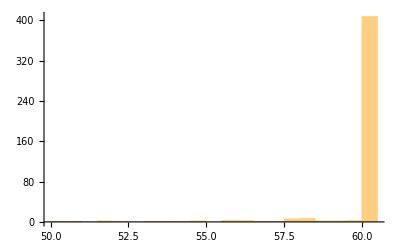

```mathematica
Histogram[fullgenomeSNPEFF[[All,133]]]
```

Many of the ones with lower mapping quality are the ones with missing genotype calls (filtered out below):

```mathematica
Select[fullgenomeSNPEFF[[All,{1,3,8,133}]],#[[4]]<60&]//MatrixForm
```

(chrI | 25487 | FLO9 | 58.61
chrI | 25489 | FLO9 | 57.62
chrI | 27090 | FLO9 | 52.4
chrI | 204218 | FLO1 | 56.97
chrI | 206360 | FLO1 | 54.5
chrI | 206363 | FLO1 | 54.41
chrI | 206375 | FLO1 | 53.78
chrV | 22913 | HXT13 | 51.91
chrVIII | 93335 | YHL008C | 58.24
chrVIII | 93350 | YHL008C | 58.24
chrVIII | 93359 | YHL008C | 58.13
chrVIII | 93361 | YHL008C | 58.11
chrVIII | 93370 | YHL008C | 58.16
chrVIII | 93375 | YHL008C | 58.16
chrVIII | 93391 | YHL008C | 58.28
chrVIII | 93577 | YHL008C | 51.63
chrVIII | 93608 | YHL008C | 54.81
chrVIII | 93624 | YHL008C | 56.2
chrVIII | 93898 | YHL008C | 50.58
chrX | 715087 | DAN4 | 58.93
chrX | 715108 | DAN4 | 57.88
chrX | 715114 | DAN4 | 57.14
chrX | 715117 | DAN4 | 59.04
chrX | 715141 | DAN4 | 55.81
chrX | 715149 | DAN4 | 59.1
chrXI | 144880 | PIR3 | 55.87
chrXI | 144883 | PIR3 | 56.03
chrXI | 578481 | YKR073C | 53.08
chrXI | 578485 | YKR073C | 50.17
chrXI | 613636 | SRP40 | 59.9
chrXII | 5683 | YLL066W-B | 57.77
chrXII | 650822 | HAP1 | 59.76
chrXIII | 588588 | MSS11 | 59.85
chrXIII | 609388 | DDR48 | 57.68
chrXIII | 908159 | YMR317W | 57.88
chrXIII | 908168 | YMR317W | 57.87
chrXIII | 908215 | YMR317W | 56.28
chrXIII | 908221 | YMR317W | 55.95)

```mathematica
Union[%[[All,3]]]
```

{DAN4,DDR48,FLO1,FLO9,HAP1,HXT13,MSS11,PIR3,SRP40,YHL008C,YKR073C,YLL066W-B,YMR317W}

Mean mapping quality of all genes:

```mathematica
Mean[fullgenomeSNPEFF[[All,133]]]
```

59.7012

Mean mapping quality of the genes dropped below with ≥5 “.” calls:

```mathematica
{"BSC1","DAN4","FLO1","FLO9","HAP1","MSS11","PIR3","YHL008C","YKR073C"};
Select[fullgenomeSNPEFF,MemberQ[%,#[[8]]]&];
Mean[%[[All,133]]]
```

56.6091

Of the genes filtered out because of having 5 or more uncalled genotypes, all but BSC1 have MQ<60

Mean mapping quality of the genes not dropped, but having some “.” calls:

```mathematica
{"SRP40","YGR130C","YLL066W-B","YLR296W","YMR317W"};
Select[fullgenomeSNPEFF,MemberQ[%,#[[8]]]&];
Mean[%[[All,133]]]
```

58.8042

Of the genes not filtered out (but of concern), three have MQ<60 {SRP40,YLL066W-B,YMR317W}.

### Dropping genes with too many uncalled or low depth (<5) genotypes

#### Processing and dropping genes with two many poor quality genotypes

Sites that were hard to call (low depth or no genotype call) can indicate duplicated genes and alignment problems.  Here we identify these:

```mathematica
droppos=-1+Position[header,"OLY077_S101"][[1,1]];(*# columns to be dropped before first sample*)
```

```mathematica
topos=Position[header,"ZnBM47_S95"][[1,1]];(*# last sample column*)
```

```mathematica
genomeSNPEFF=Table[".",{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];
```

```mathematica
genomeSNPEFF[[1]]//Length
```

110

```mathematica
fullgenomeSNPEFF[[1]]
```

{chrI,1,25487,TG,T,1492.81,GT:AD:DP:GQ:PL,FLO9,HIGH,frameshift_variant,YAL063C,c.2481delC,p.Phe827fs,T|frameshift_variant|HIGH|FLO9|YAL063C|transcript|YAL063C_mRNA|protein_coding|1/1|c.2481delC|p.Phe827fs|2481/3969|2481/3969|827/1322||,T|upstream_gene_variant|MODIFIER|YAL063C-A|YAL063C-A|transcript|YAL063C-A_mRNA|protein_coding||c.-2803delC|||||2803|,T|downstream_gene_variant|MODIFIER|YAL064W|YAL064W|transcript|YAL064W_mRNA|protein_coding||c.*3638delG|||||3638|,0:12,0:12:99:0,402,0:20,0:20:99:0,644,0:18,0:18:99:0,592,0:24,0:24:99:0,719,1:0,4:4:99:142,0,0:15,0:15:99:0,495,0:12,0:12:99:0,213,0:24,0:24:99:0,696,0:7,0:7:99:0,169,0:16,0:16:99:0,393,0:14,0:14:99:0,562,0:18,0:18:99:0,620,0:14,0:14:99:0,382,0:21,0:21:99:0,719,0:14,0:14:99:0,433,0:16,0:16:99:0,486,0:17,0:17:99:0,559,0:9,0:9:99:0,331,0:3,0:3:99:0,113,0:25,0:25:99:0,621,1:0,5:6:99:136,0,0:19,0:19:99:0,552,0:20,0:20:99:0,630,0:20,0:20:99:0,637,0:9,0:9:99:0,304,0:18,0:18:99:0,635,0:11,0:11:99:0,319,0:12,0:12:99:0,369,0:17,0:17:99:0,508,0:19,0:19:99:0,528,0:27,0:27:99:0,887,0:19,0:19:99:0,675,0:22,0:22:99:0,734,0:18,0:18:99:0,598,0:27,0:27:99:0,940,0:18,0:18:99:0,549,1:0,3:4:99:135,0,0:15,0:15:99:0,372,0:8,0:8:99:0,157,0:16,0:16:99:0,548,0:12,0:12:99:0,330,0:25,0:25:99:0,822,0:1,0:3:45:0,45,0:15,0:15:99:0,506,0:15,0:15:99:0,495,0:15,0:15:99:0,468,0:12,0:12:99:0,291,0:14,0:14:99:0,320,0:8,0:8:99:0,288,0:25,0:25:99:0,702,0:14,0:14:99:0,445,0:13,0:13:99:0,355,1:0,3:3:99:130,0,1:0,5:5:99:225,0,0:5,0:5:99:0,155,0:18,0:18:99:0,521,0:9,0:9:99:0,259,0:1,0:1:32:0,32,0:19,0:19:99:0,695,0:14,0:14:99:0,491,1:0,3:3:99:123,0,0:14,0:14:99:0,471,0:17,0:17:99:0,532,0:23,0:23:99:0,643,0:11,0:11:99:0,319,0:22,0:22:99:0,723,0:28,0:28:99:0,851,0:39,0:39:99:0,1169,0:24,0:24:99:0,593,0:27,0:27:99:0,814,0:13,0:13:99:0,450,0:6,0:6:99:0,229,0:14,0:14:99:0,245,0:12,0:12:99:0,441,0:18,0:18:99:0,602,0:22,0:22:99:0,784,0:14,0:14:99:0,405,0:22,0:22:99:0,743,0:34,0:34:99:0,1106,0:15,0:15:99:0,495,0:18,0:18:99:0,450,0:12,0:12:99:0,398,0:15,0:15:99:0,495,0:22,0:22:99:0,653,0:26,0:26:99:0,902,0:26,0:26:99:0,969,1:0,11:14:99:377,0,0:25,0:25:99:0,682,0:16,0:16:99:0,430,1:0,5:7:99:106,0,0:17,0:17:99:0,495,0:11,0:11:99:0,385,0:33,0:33:99:0,936,0:19,0:19:99:0,617,0:12,0:12:99:0,307,0:7,0:7:99:0,263,0:20,0:20:99:0,608,0:35,0:35:99:0,1113,0:25,0:25:99:0,876,0:17,0:17:99:0,524,0:12,0:12:99:0,397,0:13,0:13:99:0,409,0:16,0:16:99:0,444,0:16,0:16:99:0,517,0:13,0:13:99:0,360,0:15,0:15:99:0,385,0:35,0:35:99:0,1125,0:18,0:18:99:0,623,1:1,5:7:99:217,0,0:12,0:12:99:0,396,9,0.082,110,1.47,1799,0.,9,0.082,58.61,0.,33.17,0.792,0.846,(FLO9|YAL063C|1|1.00)}

```mathematica
For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
genomeSNPEFF[[i,j-droppos]]=temp[[1]];
]
]
```

```mathematica
genomeSNPEFF//Length
```

446

```mathematica
Tally[Select[genomeSNPEFF[[1]],#≠"."&]]
```

{{0,101},{1,9}}

All mutant sites and the tally of mutations in them:

```mathematica
summarytable=Table[{fullgenomeSNPEFF[[i,1]],fullgenomeSNPEFF[[i,3]],fullgenomeSNPEFF[[i,8]],fullgenomeSNPEFF[[i,9]],Sort[Tally[genomeSNPEFF[[i]]]]},{i,1,Length[genomeSNPEFF]}];
```

The set of sites where the number of “.” calls was ≥5:

```mathematica
dropthese=Select[summarytable,(#[[5,1,1]]==".")&&(#[[5,1,2]]≥5)&];
dropthese//MatrixForm
```

(chrI | 27090 | FLO9 | LOW | {{.,83},{0,2},{1,25}}
chrI | 204218 | FLO1 | MODERATE | {{.,71},{0,19},{1,20}}
chrI | 206360 | FLO1 | LOW | {{.,80},{0,16},{1,14}}
chrI | 206363 | FLO1 | LOW | {{.,70},{0,26},{1,14}}
chrI | 206375 | FLO1 | LOW | {{.,95},{0,1},{1,14}}
chrIV | 384924 | BSC1 | HIGH | {{.,99},{0,7},{1,4}}
chrVIII | 93335 | YHL008C | LOW | {{.,41},{0,1},{1,68}}
chrVIII | 93350 | YHL008C | LOW | {{.,39},{0,3},{1,68}}
chrVIII | 93359 | YHL008C | MODERATE | {{.,29},{0,15},{1,66}}
chrVIII | 93375 | YHL008C | HIGH | {{.,30},{0,44},{1,36}}
chrVIII | 93391 | YHL008C | MODERATE | {{.,65},{0,9},{1,36}}
chrX | 715087 | DAN4 | LOW | {{.,6},{0,97},{1,7}}
chrX | 715108 | DAN4 | LOW | {{.,65},{0,2},{1,43}}
chrX | 715114 | DAN4 | LOW | {{.,68},{0,5},{1,37}}
chrX | 715141 | DAN4 | LOW | {{.,61},{0,27},{1,22}}
chrXI | 144880 | PIR3 | LOW | {{.,76},{0,5},{1,29}}
chrXI | 144883 | PIR3 | LOW | {{.,52},{0,29},{1,29}}
chrXI | 578481 | YKR073C | HIGH | {{.,32},{0,77},{1,1}}
chrXII | 650822 | HAP1 | HIGH | {{.,90},{0,14},{1,6}}
chrXII | 650830 | HAP1 | LOW | {{.,98},{0,1},{1,11}}
chrXIII | 588588 | MSS11 | MODERATE | {{.,8},{0,25},{1,77}})

```mathematica
dropme=Union[dropthese[[All,3]]]
%//Length
```

{BSC1,DAN4,FLO1,FLO9,HAP1,MSS11,PIR3,YHL008C,YKR073C}

9

Depth of coverage for these genes is much higher on average, with both the high outliers (FLO1) and the two low outliers (BSC1 and HAP1):

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{FLO9,1799},{FLO9,1584},{FLO9,2213},{FLO1,348},{FLO1,15599},{FLO1,15734},{FLO1,17792},{BSC1,91},{YHL008C,2060},{YHL008C,2102},{YHL008C,2001},{YHL008C,1983},{YHL008C,1921},{YHL008C,1941},{YHL008C,2062},{YHL008C,1441},{YHL008C,1946},{YHL008C,1810},{YHL008C,2247},{DAN4,905},{DAN4,1522},{DAN4,1559},{DAN4,1583},{DAN4,1310},{DAN4,628},{PIR3,2648},{PIR3,2800},{YKR073C,1609},{YKR073C,1536},{HAP1,509},{HAP1,84},{MSS11,658}}

2938.28

Mapping quality is also poorer on average (except for BSC1):

```mathematica
Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]&][[All,{8,133}]]
Mean[%[[All,2]]]//N
```

{{FLO9,58.61},{FLO9,57.62},{FLO9,52.4},{FLO1,56.97},{FLO1,54.5},{FLO1,54.41},{FLO1,53.78},{BSC1,60.},{YHL008C,58.24},{YHL008C,58.24},{YHL008C,58.13},{YHL008C,58.11},{YHL008C,58.16},{YHL008C,58.16},{YHL008C,58.28},{YHL008C,51.63},{YHL008C,54.81},{YHL008C,56.2},{YHL008C,50.58},{DAN4,58.93},{DAN4,57.88},{DAN4,57.14},{DAN4,59.04},{DAN4,55.81},{DAN4,59.1},{PIR3,55.87},{PIR3,56.03},{YKR073C,53.08},{YKR073C,50.17},{HAP1,59.76},{HAP1,60.},{MSS11,59.85}}

56.6091

Dropping all sites (32) in the nine genes with ≥5 “.” calls:

```mathematica
Length[fullgenomeSNPEFF];
fullgenomeSNPEFF=Select[fullgenomeSNPEFF,MemberQ[dropme,#[[8]]]==False&];
%%-Length[fullgenomeSNPEFF]
```

32

Considering the others with uncalled genotypes, first recalculating the summary table:

```mathematica
genomeSNPEFF=Table[".",{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
genomeSNPEFF[[i,j-droppos]]=temp[[1]];
]
]
summarytable=Table[{fullgenomeSNPEFF[[i,1]],fullgenomeSNPEFF[[i,3]],fullgenomeSNPEFF[[i,8]],fullgenomeSNPEFF[[i,9]],Sort[Tally[genomeSNPEFF[[i]]]]},{i,1,Length[genomeSNPEFF]}];
```

```mathematica
consider=Select[summarytable,(#[[5,1,1]]==".")&&(#[[5,1,2]]<5)&&(#[[5,1,2]]≥1)&];
consider//MatrixForm
```

(chrVII | 753296 | YGR130C | MODERATE | {{.,1},{0,23},{1,86}}
chrXI | 613636 | SRP40 | MODERATE | {{.,1},{0,1},{1,108}}
chrXII | 5683 | YLL066W-B | HIGH | {{.,3},{0,99},{1,8}}
chrXII | 723168 | YLR296W | HIGH | {{.,2},{0,104},{1,4}}
chrXIII | 908215 | YMR317W | LOW | {{.,1},{0,17},{1,92}}
chrXIII | 908221 | YMR317W | LOW | {{.,2},{0,9},{1,99}})

```mathematica
considergenes=Union[consider[[All,3]]]
%//Length
```

{SRP40,YGR130C,YLL066W-B,YLR296W,YMR317W}

5

Depth of coverage for these genes is much higher on average, with both the high outliers (FLO1) and the two low outliers (BSC1 and HAP1):

```mathematica
Select[fullgenomeSNPEFF,MemberQ[considergenes,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{YGR130C,2020},{YGR130C,2020},{YGR130C,1799},{YGR130C,1809},{SRP40,1173},{YLL066W-B,607},{YLR296W,974},{YLR296W,977},{YMR317W,1959},{YMR317W,1960},{YMR317W,1836},{YMR317W,1789}}

1576.92

Mapping quality is also poorer on average:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[considergenes,#[[8]]]&][[All,{8,133}]]
Mean[%[[All,2]]]//N
```

{{YGR130C,60.},{YGR130C,60.},{YGR130C,60.},{YGR130C,60.},{SRP40,59.9},{YLL066W-B,57.77},{YLR296W,60.},{YLR296W,60.},{YMR317W,57.88},{YMR317W,57.87},{YMR317W,56.28},{YMR317W,55.95}}

58.8042

This is in the bottom 2% of MQ:

```mathematica
Quantile[fullgenomeSNPEFF[[All,133]],0.019]
```

59.9

These genes are kept but will be flagged as:
	{SRP40,YLL066W-B,YMR317W} have MQ<60
	{YGR130C,YMR317W} have depth ~ twice average depth (~1000)

Genes with suggestions of excessive SNP mutations include the above:

```mathematica
consider=Select[summarytable,(#[[5,1,2]]≤105)&&(#[[5,2,2]]≤105)&];
consider//MatrixForm
```

(chrIV | 815428 | NGG1 | MODERATE | {{0,100},{1,10}}
chrVII | 753296 | YGR130C | MODERATE | {{.,1},{0,23},{1,86}}
chrVII | 869872 | TFG1 | MODERATE | {{0,104},{1,6}}
chrXI | 613636 | SRP40 | MODERATE | {{.,1},{0,1},{1,108}}
chrXII | 5683 | YLL066W-B | HIGH | {{.,3},{0,99},{1,8}}
chrXII | 723168 | YLR296W | HIGH | {{.,2},{0,104},{1,4}}
chrXIII | 908159 | YMR317W | HIGH | {{0,8},{1,102}}
chrXIII | 908168 | YMR317W | HIGH | {{0,8},{1,102}}
chrXIII | 908215 | YMR317W | LOW | {{.,1},{0,17},{1,92}}
chrXIII | 908221 | YMR317W | LOW | {{.,2},{0,9},{1,99}})

```mathematica
considergenes=Union[consider[[All,3]]]
%//Length
```

{NGG1,SRP40,TFG1,YGR130C,YLL066W-B,YLR296W,YMR317W}

7

Depth of coverage for these genes is much higher on average:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[considergenes,#[[8]]]&][[All,{8,129}]]
Mean[%[[All,2]]]//N
```

{{NGG1,642},{YGR130C,2020},{YGR130C,2020},{YGR130C,1799},{YGR130C,1809},{TFG1,798},{SRP40,1173},{YLL066W-B,607},{YLR296W,974},{YLR296W,977},{YMR317W,1959},{YMR317W,1960},{YMR317W,1836},{YMR317W,1789}}

1454.5

Mapping quality is also poorer on average:

```mathematica
Select[fullgenomeSNPEFF,MemberQ[considergenes,#[[8]]]&][[All,{8,133}]]
Mean[%[[All,2]]]//N
```

{{NGG1,60.},{YGR130C,60.},{YGR130C,60.},{YGR130C,60.},{YGR130C,60.},{TFG1,60.},{SRP40,59.9},{YLL066W-B,57.77},{YLR296W,60.},{YLR296W,60.},{YMR317W,57.88},{YMR317W,57.87},{YMR317W,56.28},{YMR317W,55.95}}

58.975

#### Revised gene list

```mathematica
genelist=Sort[Union[fullgenomeSNPEFF[[All,8]]]]
Length[%]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YIH1,YIL092W,YLL066W-B,YLR108C,YLR296W,YML119W,YMR027W,YMR317W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

333

Plotting the depth of coverage at that site:

```mathematica
Mean[fullgenomeSNPEFF[[All,129]]]//N
```

933.978

```mathematica
Max[fullgenomeSNPEFF[[All,129]]]
```

2469

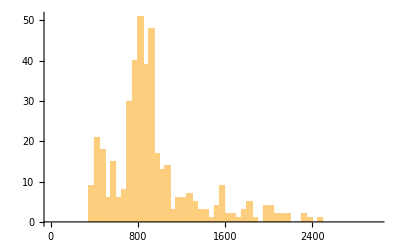

```mathematica
Histogram[fullgenomeSNPEFF[[All,129]],{50},PlotRange->{{0,3000},Automatic}]
```

#### Exporting

For printing, we want a shorter header table:

```mathematica
newheader=Table[StringSplit[header[[i]],"_"][[1]],{i,1,Length[header]}]
```

{CHROM,chr,POS,REF,ALT,QUAL,FORMAT,gene,effect,mut,gene,base,aa,ANN,OLY077,CdBM23,CdBM25,CdBM26,CdBM29,CdBM30,CdBM32,CdBM36,CdBM37,CdBM39,CdBM42,CdBM43,CdBM44,CdBM45,CdBM46,CdBM47,CdBM48,CoBM12,CoBM14,CoBM15,CoBM16,CoBM17,CoBM18,CoBM1,CoBM20,CoBM21,CoBM2,CoBM3,CoBM4,CoBM5,CoBM6,CoBM7,CoBM8,CuBM10,CuBM11,CuBM12,CuBM13,CuBM14,CuBM15,CuBM16,CuBM17,CuBM18,CuBM3,CuBM4,CuBM6,CuBM7,CuBM8,CuBM9,MnBM12,MnBM13,MnBM14,MnBM15,MnBM16,MnBM17,MnBM18,MnBM20,MnBM21,MnBM23,MnBM24,MnBM25,MnBM27,MnBM28,MnBM29,MnBM31,MnBM32,MnBM34,MnBM38,MnBM39,MnBM42,MnBM44,NiBM11,NiBM12,NiBM14,NiBM16,NiBM17,NiBM21,NiBM22,NiBM24,NiBM25,NiBM27,NiBM28,NiBM29,NiBM30,NiBM4,NiBM6,NiBM8,NiBM9,ZnBM11,ZnBM12,ZnBM15,ZnBM16,ZnBM17,ZnBM19,ZnBM22,ZnBM23,ZnBM25,ZnBM28,ZnBM29,ZnBM31,ZnBM34,ZnBM37,ZnBM38,ZnBM39,ZnBM41,ZnBM42,ZnBM43,ZnBM44,ZnBM45,ZnBM46,ZnBM47,AC,AF,AN,BaseQRankSum,DP,FS,MLEAC,MLEAF,MQ,MQRankSum,QD,ReadPosRankSum,SOR,LOF}

First recalculating the summary table:

```mathematica
genomeSNPEFF=Table[-1,{i,1,Length[fullgenomeSNPEFF]},{j,1,topos-droppos}];For[i=1,i≤Length[fullgenomeSNPEFF],i++,
For[j=1+droppos,j≤topos,j++,
temp=StringSplit[fullgenomeSNPEFF[[i,j]],{":"}];
temp2=temp[[1]];
genomeSNPEFF[[i,j-droppos]]=temp2;
]
]
```

The following sites are “1”s in OLY077 and so we swap 1’s for 0’s and call these revertants

```mathematica
Position[genomeSNPEFF,_?(#[[1]]=="1"&)][[All,1]]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{155,234,322,323,324,325}

Swapping 0<->1 and calling “.” 0 (like OLY077):

```mathematica
For[i=1,i≤Length[%],i++,
genomeSNPEFF[[%[[i]]]]=Mod[ToExpression[StringReplace[genomeSNPEFF[[%[[i]]]],"."->"1"]]+1,2]
]
```

Swapped variants positions:

```mathematica
fullgenomeSNPEFF[[%%,{1,3,8}]]
```

{{chrVII,753296,YGR130C},{chrXI,613636,SRP40},{chrXIII,908159,YMR317W},{chrXIII,908168,YMR317W},{chrXIII,908215,YMR317W},{chrXIII,908221,YMR317W}}

All remaining “.” are treated as identical to OLY077 (not mutant) and 0/1 treated as numbers (only in genomeSNPEFF, summarytable and fullgenomeSNPEFF remain the same):

```mathematica
genomeSNPEFF=genomeSNPEFF/."."->"0";
genomeSNPEFF=ToExpression/@genomeSNPEFF;
```

Number of unique mutations:

```mathematica
Length[genomeSNPEFF]
```

414

Number of mutational hits:

```mathematica
Total[Total[genomeSNPEFF]]
```

523

As expected (once revertants were recoded), OLY077 has no mutations

```mathematica
Total[genomeSNPEFF[[All,1]]]
```

0

Number of lines per unique mutation:

```mathematica
Sort[Tally[Sum[genomeSNPEFF[[All,i]],{i,1,110}]]]
```

{{1,384},{2,18},{3,2},{4,2},{6,1},{8,3},{9,1},{10,1},{17,1},{23,1}}

Genes with excessive SNP mutations include:

```mathematica
toopoly=Position[genomeSNPEFF,_?(Total[#]>5&)][[All,1]]
```

{68,155,159,236,322,323,324,325}

The genotype call for OLY077:

```mathematica
fullgenomeSNPEFF[[toopoly,Position[newheader,"OLY077"][[1,1]]]]//MatrixForm
```

(0:3,0:3:99:0,100
1:0,21:21:99:945,0
0:8,0:8:99:0,175
0:13,0:13:99:0,226
1:0,10:10:99:450,0
1:0,10:10:99:450,0
1:0,9:9:99:406,0
1:0,9:9:99:406,0)

```mathematica
consider=summarytable[[toopoly]];
consider//MatrixForm
```

(chrIV | 815428 | NGG1 | MODERATE | {{0,100},{1,10}}
chrVII | 753296 | YGR130C | MODERATE | {{.,1},{0,23},{1,86}}
chrVII | 869872 | TFG1 | MODERATE | {{0,104},{1,6}}
chrXII | 5683 | YLL066W-B | HIGH | {{.,3},{0,99},{1,8}}
chrXIII | 908159 | YMR317W | HIGH | {{0,8},{1,102}}
chrXIII | 908168 | YMR317W | HIGH | {{0,8},{1,102}}
chrXIII | 908215 | YMR317W | LOW | {{.,1},{0,17},{1,92}}
chrXIII | 908221 | YMR317W | LOW | {{.,2},{0,9},{1,99}})

Depth of coverage for these genes is higher on average:

```mathematica
fullgenomeSNPEFF[[toopoly,{8,129}]]
Mean[%[[All,2]]]//N
```

{{NGG1,642},{YGR130C,1809},{TFG1,798},{YLL066W-B,607},{YMR317W,1959},{YMR317W,1960},{YMR317W,1836},{YMR317W,1789}}

1425.

Mapping quality is also poorer on average:

```mathematica
fullgenomeSNPEFF[[toopoly,{8,133}]]
Mean[%[[All,2]]]//N
```

{{NGG1,60.},{YGR130C,60.},{TFG1,60.},{YLL066W-B,57.77},{YMR317W,57.88},{YMR317W,57.87},{YMR317W,56.28},{YMR317W,55.95}}

58.2188

Ones below 60 are in the bottom 2% of MQ:

```mathematica
Quantile[fullgenomeSNPEFF[[All,133]],0.019]
```

59.9

```mathematica
considergenes=Union[consider[[All,3]]]
%//Length
```

{NGG1,TFG1,YGR130C,YLL066W-B,YMR317W}

5

```mathematica
toprintmultiple=Sort[Table[{fullgenomeSNPEFF[[toopoly[[i]],8]],fullgenomeSNPEFF[[toopoly[[i]],11]],StringJoin[fullgenomeSNPEFF[[toopoly[[i]],1]],".",ToString[fullgenomeSNPEFF[[toopoly[[i]],3]]]],fullgenomeSNPEFF[[toopoly[[i]],12]],fullgenomeSNPEFF[[toopoly[[i]],13]],summarytable[[toopoly[[i]],5]],genomeSNPEFF[[toopoly[[i]]]].newheader[[1+droppos;;topos]]},{i,1,Length[toopoly]}]];
MatrixForm[%]
```

(NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn | {{0,100},{1,10}} | CuBM10+CuBM11+CuBM12+CuBM13+CuBM14+CuBM17+CuBM18+CuBM4+CuBM7+CuBM9
TFG1 | YGR186W | chrVII.869872 | c.2099T>C | p.Phe700Ser | {{0,104},{1,6}} | CuBM11+CuBM14+CuBM17+CuBM18+CuBM7+CuBM9
YGR130C | YGR130C | chrVII.753296 | c.543_548delATCGTC | p.Ser182_Ser183del | {{.,1},{0,23},{1,86}} | CdBM23+CdBM36+CdBM39+CdBM43+CoBM12+CoBM15+CoBM16+CoBM17+CoBM20+CuBM12+CuBM9+MnBM17+MnBM21+MnBM25+MnBM29+NiBM12+NiBM14+NiBM22+NiBM8+NiBM9+ZnBM17+ZnBM22+ZnBM23
YLL066W-B | YLL066W-B | chrXII.5683 | c.85_103delCACACCCACACCCACACAC | p.His29fs | {{.,3},{0,99},{1,8}} | CdBM42+MnBM20+MnBM23+NiBM21+ZnBM28+ZnBM34+ZnBM41+ZnBM44
YMR317W | YMR317W | chrXIII.908159 | c.797_804delCGGCAACG | p.Ser266fs | {{0,8},{1,102}} | CdBM29+CdBM36+CoBM14+CuBM13+CuBM6+MnBM16+MnBM17+MnBM24
YMR317W | YMR317W | chrXIII.908168 | c.806_833delCTAGCGTAATTAGTTCAGAAGCTTCATG | p.Ser269fs | {{0,8},{1,102}} | CdBM29+CdBM36+CoBM14+CuBM13+CuBM6+MnBM16+MnBM17+MnBM24
YMR317W | YMR317W | chrXIII.908215 | c.852G>A | p.Val284Val | {{.,1},{0,17},{1,92}} | CdBM23+CdBM29+CdBM32+CdBM36+CdBM43+CoBM14+CoBM7+CoBM8+CuBM10+CuBM13+CuBM6+CuBM9+MnBM12+MnBM16+MnBM17+MnBM23+NiBM24
YMR317W | YMR317W | chrXIII.908221 | c.858G>A | p.Ser286Ser | {{.,2},{0,9},{1,99}} | CdBM23+CdBM36+CoBM14+CuBM10+CuBM13+CuBM6+CuBM9+MnBM16+MnBM23)

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/toopolymorphic_8Nov2024.tsv",toprintmultiple];
```

The remaining sites:

```mathematica
rest=Complement[Table[i,{i,1,Length[fullgenomeSNPEFF]}],toopoly];
```

```mathematica
Length[rest]+Length[toopoly]-Length[fullgenomeSNPEFF]
```

0

Including NGG1 and TFG1:

```mathematica
fullgenomeSNPEFF[[68,8]]
```

NGG1

```mathematica
fullgenomeSNPEFF[[159,8]]
```

TFG1

```mathematica
rest=Sort[Join[rest,{68,159}]];
```

```mathematica
toprint=Table[{fullgenomeSNPEFF[[rest[[i]],8]],fullgenomeSNPEFF[[rest[[i]],11]],StringJoin[fullgenomeSNPEFF[[rest[[i]],1]],".",ToString[fullgenomeSNPEFF[[rest[[i]],3]]]],fullgenomeSNPEFF[[rest[[i]],12]],fullgenomeSNPEFF[[rest[[i]],13]],genomeSNPEFF[[rest[[i]]]].newheader[[1+droppos;;topos]]},{i,1,Length[rest]}];
MatrixForm[%[[1;;12]]] (*The first 12 lines shows the nature of parallel SNPs in different lines*)
```

(CNE1 | YAL058W | chrI.37834 | c.371C>T | p.Thr124Met | MnBM14
CNE1 | YAL058W | chrI.38041 | c.578C>T | p.Ser193Leu | MnBM14
GPB2 | YAL056W | chrI.40593 | c.1335A>C | p.Leu445Phe | CoBM17
FLC2 | YAL053W | chrI.48206 | c.2308A>G | p.Asn770Asp | MnBM14
OAF1 | YAL051W | chrI.48640 | c.77C>T | p.Ala26Val | MnBM14
CLN3 | YAL040C | chrI.66785 | c.736T>G | p.Leu246Val | CoBM3
CCR4 | YAL021C | chrI.112637 | c.723C>G | p.Asp241Glu | MnBM42
CCR4 | YAL021C | chrI.113278 | c.82C>T | p.Leu28Leu | MnBM42
SHP1 | YBL058W | chrII.112395 | c.959A>T | p.Glu320Val | CoBM6
COQ1 | YBR003W | chrII.243326 | c.518C>A | p.Pro173His | CuBM15
RKM3 | YBR030W | chrII.299270 | c.979G>C | p.Gly327Arg | CoBM4+NiBM24
IST2 | YBR086C | chrII.421076 | c.1966G>T | p.Ala656Ser | NiBM12)

```mathematica
Length[toprint]
```

408

For each SNP that occurs multiple times, make a separate row:

```mathematica
For[i=1;toappend={},i≤Length[toprint],i++,
splits=Length[toprint[[i,6]]];
If[splits>1,
temp=toprint[[i,6]];
toprint[[i,6]]=toprint[[i,6]][[1]];
For[j=2,j≤splits,j++,
toadd=toprint[[i]];
toadd[[6]]=temp[[j]];
toappend=Append[toappend,toadd]
]
]
]
```

Sorting then putting the metal first:

```mathematica
Sort[Join[toprint,toappend]];
mat=Transpose[Join[{Transpose[%[[All,6]]]},Transpose[%[[All,1;;5]]]]];
MatrixForm[mat]
```

(CuBM18 | ABP1 | YCR088W | chrIII.265691 | c.624A>C | p.Leu208Phe
MnBM42 | ACB1 | YGR037C | chrVII.559830 | c.165G>A | p.Lys55Lys
ZnBM12 | ACC1 | YNR016C | chrXIV.660428 | c.947G>T | p.Gly316Val
ZnBM15 | ACC1 | YNR016C | chrXIV.660428 | c.947G>T | p.Gly316Val
ZnBM23 | ADE6 | YGR061C | chrVII.613265 | c.2701G>C | p.Val901Leu
MnBM23 | ADR1 | YDR216W | chrIV.896208 | c.1174C>T | p.His392Tyr
CoBM17 | AFT1 | YGL071W | chrVII.372520 | c.509C>T | p.Ser170Phe
MnBM31 | AGP1 | YCL025C | chrIII.76154 | c.1765delA | p.Ile589fs
MnBM31 | AGP1 | YCL025C | chrIII.76159 | c.1761G>T | p.Leu587Leu
CdBM25 | AHK1 | YDL073W | chrIV.329143 | c.2531G>A | p.Gly844Glu
MnBM18 | ALD5 | YER073W | chrV.304100 | c.71C>A | p.Ser24Tyr
CoBM16 | ALY2 | YJL084C | chrX.277922 | c.80delT | p.Leu27fs
CoBM2 | APC2 | YLR127C | chrXII.397423 | c.897G>A | p.Lys299Lys
MnBM23 | ARO3 | YDR035W | chrIV.522083 | c.268G>A | p.Glu90Lys
CoBM18 | ASN1 | YPR145W | chrXVI.822877 | c.258A>C | p.Glu86Asp
MnBM42 | ATG11 | YPR049C | chrXVI.662014 | c.2660G>T | p.Arg887Ile
CuBM6 | ATG2 | YNL242W | chrXIV.195289 | c.3966A>G | p.Leu1322Leu
CoBM5 | ATG39 | YLR312C | chrXII.757873 | c.961T>C | p.Tyr321His
MnBM42 | BDS1 | YOL164W | chrXV.7199 | c.1025C>T | p.Thr342Ile
MnBM18 | BIR1 | YJR089W | chrX.588774 | c.1057C>T | p.Arg353Cys
CuBM7 | BLM10 | YFL007W | chrVI.127204 | c.3726C>T | p.His1242His
CdBM44 | BNA6 | YFR047C | chrVI.245165 | c.1delA | p.Met1fs
CoBM2 | BNI1 | YNL271C | chrXIV.132973 | c.2411C>G | p.Thr804Ser
MnBM39 | BNI4 | YNL233W | chrXIV.214433 | c.2512A>T | p.Ile838Leu
MnBM42 | BRR2 | YER172C | chrV.533465 | c.2557T>A | p.Tyr853Asn
NiBM24 | BSD2 | YBR290W | chrII.783212 | c.622C>T | p.Gln208*
NiBM11 | BSD2 | YBR290W | chrII.783400 | c.810G>T | p.Leu270Phe
ZnBM11 | BSD2 | YBR290W | chrII.783400 | c.810G>T | p.Leu270Phe
CuBM14 | BUL1 | YMR275C | chrXIII.817667 | c.915G>T | p.Met305Ile
CoBM7 | BUL2 | YML111W | chrXIII.48465 | c.1524T>A | p.Asn508Lys
MnBM42 | CAJ1 | YER048C | chrV.247483 | c.675G>A | p.Glu225Glu
CoBM3 | CCC2 | YDR270W | chrIV.1005804 | c.130G>T | p.Val44Leu
MnBM42 | CCR4 | YAL021C | chrI.112637 | c.723C>G | p.Asp241Glu
MnBM42 | CCR4 | YAL021C | chrI.113278 | c.82C>T | p.Leu28Leu
MnBM31 | CCW12 | YLR110C | chrXII.369713 | c.386C>A | p.Ala129Asp
MnBM21 | CDC25 | YLR310C | chrXII.752946 | c.4047delA | p.Lys1349fs
MnBM25 | CDC25 | YLR310C | chrXII.753045 | c.3949G>T | p.Glu1317*
MnBM18 | CDC25 | YLR310C | chrXII.753381 | c.3589_3612delGTCAACATTATGAGAACATTTTTG | p.Val1197_Leu1204del
MnBM23 | CDC25 | YLR310C | chrXII.755637 | c.1357T>A | p.Tyr453Asn
MnBM23 | CDC25 | YLR310C | chrXII.755641 | c.1353T>A | p.Tyr451*
MnBM24 | CDC25 | YLR310C | chrXII.755784 | c.1210A>T | p.Asn404Tyr
MnBM24 | CDC25 | YLR310C | chrXII.755785 | c.1209T>A | p.Asn403Lys
MnBM24 | CDC25 | YLR310C | chrXII.755790 | c.1203delT | p.Asp401fs
MnBM27 | CDC25 | YLR310C | chrXII.755841 | c.1152dupA | p.Gln385fs
MnBM20 | CDC25 | YLR310C | chrXII.755855 | c.1139T>A | p.Leu380His
MnBM20 | CDC25 | YLR310C | chrXII.755857 | c.1136delG | p.Ser379fs
MnBM15 | CDC25 | YLR310C | chrXII.755928 | c.1065delG | p.Arg356fs
MnBM32 | CDC25 | YLR310C | chrXII.756549 | c.444delG | p.Arg148fs
MnBM14 | CIC1 | YHR052W | chrVIII.211267 | c.420A>G | p.Leu140Leu
MnBM14 | CLB3 | YDL155W | chrIV.178021 | c.1249G>A | p.Ala417Thr
CoBM3 | CLN3 | YAL040C | chrI.66785 | c.736T>G | p.Leu246Val
MnBM14 | CNE1 | YAL058W | chrI.37834 | c.371C>T | p.Thr124Met
MnBM14 | CNE1 | YAL058W | chrI.38041 | c.578C>T | p.Ser193Leu
MnBM38 | COG1 | YGL223C | chrVII.80104 | c.262A>T | p.Thr88Ser
MnBM42 | COG3 | YER157W | chrV.485939 | c.1152G>T | p.Arg384Ser
MnBM27 | COI1 | YDR381C-A | chrIV.1238427 | c.230G>T | p.Cys77Phe
NiBM6 | COI1 | YDR381C-A | chrIV.1238427 | c.230G>T | p.Cys77Phe
CuBM15 | COQ1 | YBR003W | chrII.243326 | c.518C>A | p.Pro173His
MnBM42 | CPA1 | YOR303W | chrXV.882919 | c.21A>G | p.Lys7Lys
CdBM30 | CSM3 | YMR048W | chrXIII.367082 | c.102T>C | p.Asp34Asp
MnBM42 | CUE3 | YGL110C | chrVII.302721 | c.691A>T | p.Lys231*
MnBM42 | CWC22 | YGR278W | chrVII.1047684 | c.954G>A | p.Ala318Ala
MnBM42 | CWH41 | YGL027C | chrVII.444280 | c.1864G>C | p.Val622Leu
CdBM23 | CYK3 | YDL117W | chrIV.249010 | c.437delA | p.Asn146fs
CdBM39 | CYK3 | YDL117W | chrIV.249010 | c.437delA | p.Asn146fs
MnBM42 | DAL2 | YIR029W | chrIX.411668 | c.862T>A | p.Ser288Thr
CdBM30 | DBF20 | YPR111W | chrXVI.747862 | c.567delA | p.Asp190fs
ZnBM16 | DBP10 | YDL031W | chrIV.396323 | c.2107A>T | p.Met703Leu
CdBM42 | DDR48 | YMR173W | chrXIII.609388 | c.700A>G | p.Asn234Asp
CuBM6 | DNF1 | YER166W | chrV.513891 | c.1148G>C | p.Arg383Thr
CdBM30 | DNF1 | YER166W | chrV.516594 | c.3860dupT | p.Tyr1289fs
ZnBM19 | DOA4 | YDR069C | chrIV.587104 | c.616C>T | p.Gln206*
MnBM42 | DOT6 | YER088C | chrV.334086 | c.1103C>A | p.Ser368Tyr
MnBM42 | DSC2 | YOL073C | chrXV.194233 | c.568T>C | p.Leu190Leu
MnBM12 | DSE4 | YNR067C | chrXIV.757064 | c.2036G>A | p.Gly679Asp
CoBM6 | DUS4 | YLR405W | chrXII.930419 | c.631C>T | p.Leu211Leu
CoBM8 | EBS1 | YDR206W | chrIV.864180 | c.2127A>T | p.Glu709Asp
ZnBM16 | ECM14 | YHR132C | chrVIII.369079 | c.716G>C | p.Trp239Ser
MnBM42 | ECM22 | YLR228C | chrXII.600763 | c.1701C>T | p.Tyr567Tyr
CdBM32 | EFR3 | YMR212C | chrXIII.692578 | c.465delT | p.Phe155fs
ZnBM28 | ELO3 | YLR372W | chrXII.868274 | c.921C>A | p.Tyr307*
CdBM30 | ERB1 | YMR049C | chrXIII.369659 | c.859C>A | p.Arg287Ser
CoBM4 | ERG1 | YGR175C | chrVII.848366 | c.58G>T | p.Asp20Tyr
MnBM12 | ERG27 | YLR100W | chrXII.341936 | c.127C>A | p.Pro43Thr
MnBM14 | ERG7 | YHR072W | chrVIII.240532 | c.1435C>T | p.His479Tyr
MnBM17 | ERG9 | YHR190W | chrVIII.484871 | c.27G>A | p.Leu9Leu
MnBM42 | FAS2 | YPL231W | chrXVI.110829 | c.2178T>C | p.Gly726Gly
MnBM42 | FAU1 | YER183C | chrV.553782 | c.188T>G | p.Ile63Ser
NiBM30 | FCY2 | YER056C | chrV.266649 | c.1465C>T | p.Gln489*
CdBM32 | FET4 | YMR319C | chrXIII.912911 | c.1628G>C | p.Arg543Pro
CdBM42 | FET4 | YMR319C | chrXIII.914235 | c.303delT | p.Phe101fs
MnBM14 | FIG2 | YCR089W | chrIII.270029 | c.2596G>A | p.Ala866Thr
CuBM14 | FIG4 | YNL325C | chrXIV.29337 | c.2042G>A | p.Arg681Lys
MnBM14 | FLC2 | YAL053W | chrI.48206 | c.2308A>G | p.Asn770Asp
MnBM42 | FMP52 | YER004W | chrV.159636 | c.57C>T | p.His19His
MnBM38 | FRE6 | YLL051C | chrXII.37938 | c.1534A>G | p.Ser512Gly
CoBM15 | FSF1 | YOR271C | chrXV.831557 | c.486T>C | p.Gly162Gly
MnBM13 | FYV10 | YIL097W | chrIX.181615 | c.1189C>T | p.His397Tyr
CoBM3 | FYV10 | YIL097W | chrIX.181770 | c.1344A>C | p.Leu448Phe
MnBM14 | FYV6 | YNL133C | chrXIV.374578 | c.115C>T | p.Gln39*
MnBM29 | FZF1 | YGL254W | chrVII.22857 | c.554T>A | p.Leu185His
MnBM42 | GAS4 | YOL132W | chrXV.72169 | c.870A>G | p.Ser290Ser
MnBM32 | GAT1 | YFL021W | chrVI.96312 | c.347C>T | p.Ala116Val
CoBM17 | GCD2 | YGR083C | chrVII.644958 | c.1858A>T | p.Thr620Ser
MnBM42 | GID12 | YDL176W | chrIV.143605 | c.1509T>G | p.Tyr503*
MnBM38 | GPB1 | YOR371C | chrXV.1033961 | c.222A>G | p.Lys74Lys
CoBM17 | GPB2 | YAL056W | chrI.40593 | c.1335A>C | p.Leu445Phe
MnBM42 | GPH1 | YPR160W | chrXVI.862883 | c.1578C>A | p.Phe526Leu
MnBM42 | GSC2 | YGR032W | chrVII.550683 | c.2420G>T | p.Arg807Met
MnBM29 | HBT1 | YDL223C | chrIV.58214 | c.2192C>A | p.Thr731Lys
MnBM42 | HEH2 | YDR458C | chrIV.1381715 | c.332A>G | p.Asp111Gly
CoBM1 | HHF2 | YNL030W | chrXIV.577027 | c.302_*4delTCGGTGGTTAAACAA | p.Phe101fs
ZnBM38 | HHF2 | YNL030W | chrXIV.577027 | c.302_*4delTCGGTGGTTAAACAA | p.Phe101fs
ZnBM31 | HIS4 | YCL030C | chrIII.66139 | c.2195C>T | p.Thr732Ile
CdBM26 | HMF1 | YER057C | chrV.270774 | c.353A>G | p.Asp118Gly
CdBM32 | HO | YDL227C | chrIV.46589 | c.1442delA | p.Lys481fs
MnBM14 | HOB2 | YPR117W | chrXVI.765419 | c.5395A>T | p.Thr1799Ser
MnBM42 | HRT3 | YLR097C | chrXII.337183 | c.83G>T | p.Gly28Val
CoBM2 | HSL1 | YKL101W | chrXI.249736 | c.817A>C | p.Thr273Pro
ZnBM44 | HSP104 | YLL026W | chrXII.90370 | c.1748A>T | p.Gln583Leu
MnBM42 | HUL5 | YGL141W | chrVII.239990 | c.1638G>T | p.Trp546Cys
CdBM45 | HUL5 | YGL141W | chrVII.240693 | c.2341G>A | p.Glu781Lys
CdBM46 | HUL5 | YGL141W | chrVII.240693 | c.2341G>A | p.Glu781Lys
CdBM47 | HUL5 | YGL141W | chrVII.240693 | c.2341G>A | p.Glu781Lys
CdBM30 | HUL5 | YGL141W | chrVII.240739 | c.2387G>A | p.Arg796Lys
MnBM32 | HXT13 | YEL069C | chrV.22913 | c.319C>T | p.Arg107Cys
NiBM6 | IDP1 | YDL066W | chrIV.334907 | c.73C>A | p.Pro25Thr
MnBM42 | IES3 | YLR052W | chrXII.247694 | c.494T>A | p.Leu165Gln
MnBM32 | ILV2 | YMR108W | chrXIII.484091 | c.8G>A | p.Arg3Lys
MnBM42 | IMA1 | YGR287C | chrVII.1068655 | c.337T>C | p.Cys113Arg
CdBM44 | INP2 | YMR163C | chrXIII.585173 | c.1215delA | p.Lys405fs
CoBM15 | IOC4 | YMR044W | chrXIII.356311 | c.928C>A | p.Pro310Thr
MnBM42 | IPI3 | YNL182C | chrXIV.297316 | c.312C>T | p.Asp104Asp
MnBM42 | IRC20 | YLR247C | chrXII.633065 | c.290C>T | p.Ala97Val
MnBM42 | IRC8 | YJL051W | chrX.340621 | c.835G>T | p.Val279Phe
NiBM12 | IST2 | YBR086C | chrII.421076 | c.1966G>T | p.Ala656Ser
MnBM32 | ISU1 | YPL135W | chrXVI.297897 | c.345G>A | p.Leu115Leu
MnBM42 | ITC1 | YGL133W | chrVII.259225 | c.1519A>T | p.Ser507Cys
CoBM21 | KAR3 | YPR141C | chrXVI.815942 | c.1982A>T | p.His661Leu
MnBM42 | KGD1 | YIL125W | chrIX.124369 | c.1681T>G | p.Phe561Val
CdBM29 | KIN1 | YDR122W | chrIV.694840 | c.157_159delCAG | p.Gln53del
CdBM30 | KIN82 | YCR091W | chrIII.275091 | c.694delC | p.Leu232fs
MnBM38 | KRE5 | YOR336W | chrXV.952618 | c.2846C>G | p.Ser949*
CoBM12 | KSP1 | YHR082C | chrVIII.268511 | c.3038G>C | p.Gly1013Ala
CuBM9 | KSP1 | YHR082C | chrVIII.271417 | c.132T>G | p.Val44Val
CdBM23 | KTR3 | YBR205W | chrII.634214 | c.593G>A | p.Trp198*
CdBM43 | KTR3 | YBR205W | chrII.634214 | c.593G>A | p.Trp198*
MnBM14 | LAM1 | YHR155W | chrVIII.407313 | c.211C>T | p.Gln71*
MnBM14 | LAM1 | YHR155W | chrVIII.407513 | c.411C>T | p.Asn137Asn
MnBM42 | LAM6 | YLR072W | chrXII.279869 | c.1008C>A | p.Ser336Ser
NiBM24 | LOS1 | YKL205W | chrXI.53317 | c.3267A>G | p.Val1089Val
MnBM17 | LRG1 | YDL240W | chrIV.23136 | c.314T>G | p.Leu105Trp
MnBM13 | MAM3 | YOL060C | chrXV.214417 | c.1720delA | p.Thr574fs
MnBM31 | MAM3 | YOL060C | chrXV.214417 | c.1720delA | p.Thr574fs
MnBM16 | MAM3 | YOL060C | chrXV.214928 | c.1209delG | p.Leu405fs
MnBM17 | MAM3 | YOL060C | chrXV.215066 | c.1072G>T | p.Glu358*
CoBM12 | MAM3 | YOL060C | chrXV.215342 | c.796T>C | p.Phe266Leu
CoBM18 | MAM3 | YOL060C | chrXV.215920 | c.218T>G | p.Leu73Arg
CoBM16 | MAS2 | YHR024C | chrVIII.158818 | c.375T>A | p.Pro125Pro
CoBM18 | MCK1 | YNL307C | chrXIV.57472 | c.102G>A | p.Leu34Leu
MnBM42 | MCM5 | YLR274W | chrXII.693876 | c.2322T>C | p.Gly774Gly
CoBM6 | MCT1 | YOR221C | chrXV.756662 | c.897C>T | p.Phe299Phe
MnBM42 | MDH2 | YOL126C | chrXV.82001 | c.920G>A | p.Gly307Glu
CoBM12 | MDL2 | YPL270W | chrXVI.30675 | c.194G>T | p.Arg65Ile
MnBM14 | MDM30 | YLR368W | chrXII.858040 | c.501C>T | p.Tyr167Tyr
MnBM16 | MET10 | YFR030W | chrVI.216146 | c.2835C>T | p.Ile945Ile
CdBM26 | MET30 | YIL046W | chrIX.269753 | c.1103A>C | p.Asn368Thr
MnBM42 | MEX67 | YPL169C | chrXVI.229047 | c.1792C>T | p.Gln598*
MnBM42 | MHP1 | YJL042W | chrX.362671 | c.1423G>T | p.Glu475*
MnBM14 | MKT1 | YNL085W | chrXIV.469502 | c.2372G>A | p.Arg791Lys
MnBM14 | MLF3 | YNL074C | chrXIV.487720 | c.405A>T | p.Ser135Ser
MnBM42 | MLH3 | YPL164C | chrXVI.241077 | c.421A>G | p.Ile141Val
CdBM47 | MLS1 | YNL117W | chrXIV.407160 | c.803A>G | p.Gln268Arg
CuBM9 | MMS4 | YBR098W | chrII.442065 | c.551G>C | p.Ser184Thr
MnBM42 | MNN9 | YPL050C | chrXVI.461357 | c.610G>T | p.Asp204Tyr
MnBM42 | MOT1 | YPL082C | chrXVI.399531 | c.4553C>T | p.Pro1518Leu
MnBM17 | MPA43 | YNL249C | chrXIV.180823 | c.200A>G | p.Gln67Arg
MnBM42 | MRL1 | YPR079W | chrXVI.699233 | c.365G>A | p.Cys122Tyr
MnBM42 | MRPL36 | YBR122C | chrII.484228 | c.276T>C | p.Ala92Ala
MnBM27 | MSC6 | YOR354C | chrXV.1001702 | c.1524T>G | p.Asn508Lys
MnBM32 | MSS2 | YDL107W | chrIV.269200 | c.280G>A | p.Asp94Asn
MnBM14 | MSS2 | YDL107W | chrIV.269955 | c.1035G>A | p.Leu345Leu
MnBM42 | MTR4 | YJL050W | chrX.342637 | c.116A>G | p.Gln39Arg
CdBM44 | MYG1 | YER156C | chrV.483851 | c.491G>A | p.Ser164Asn
CdBM26 | MYO2 | YOR326W | chrXV.929249 | c.3529G>T | p.Gly1177Cys
NiBM21 | NAM8 | YHR086W | chrVIII.278622 | c.470T>C | p.Val157Ala
MnBM14 | NAR1 | YNL240C | chrXIV.199110 | c.868C>T | p.Arg290*
CoBM6 | NFT1 | YKR103W | chrXI.655246 | c.2167A>G | p.Ile723Val
CuBM10 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM11 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM12 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM13 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM14 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM17 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM18 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM4 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM7 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
CuBM9 | NGG1 | YDR176W | chrIV.815428 | c.977G>A | p.Ser326Asn
MnBM42 | NIP100 | YPL174C | chrXVI.222669 | c.105A>C | p.Glu35Asp
MnBM23 | NPL3 | YDR432W | chrIV.1329113 | c.331C>A | p.Arg111Ser
CoBM8 | NSR1 | YGR159C | chrVII.806709 | c.948C>T | p.Ser316Ser
MnBM42 | NUC1 | YJL208C | chrX.40977 | c.207T>A | p.His69Gln
CoBM12 | NUG1 | YER006W | chrV.164204 | c.1482A>T | p.Lys494Asn
MnBM14 | OAF1 | YAL051W | chrI.48640 | c.77C>T | p.Ala26Val
CoBM21 | OCA4 | YCR095C | chrIII.288718 | c.541G>A | p.Glu181Lys
CoBM14 | OCA5 | YHL029C | chrVIII.47582 | c.387C>G | p.Tyr129*
MnBM42 | OPI1 | YHL020C | chrVIII.66824 | c.633C>T | p.Ser211Ser
MnBM42 | OSH2 | YDL019C | chrIV.417674 | c.3841G>A | p.Asp1281Asn
CdBM29 | PBP2 | YBR233W | chrII.683908 | c.481G>A | p.Gly161Arg
ZnBM23 | PBS2 | YJL128C | chrX.178468 | c.1636G>C | p.Asp546His
ZnBM39 | PBS2 | YJL128C | chrX.178937 | c.1167G>T | p.Lys389Asn
MnBM14 | PCL5 | YHR071W | chrVIII.237545 | c.542C>T | p.Pro181Leu
MnBM42 | PDA1 | YER178W | chrV.546977 | c.161A>G | p.Gln54Arg
CuBM17 | PDR1 | YGL013C | chrVII.469242 | c.3054_3056dupCAA | p.Asn1019dup
MnBM39 | PDR1 | YGL013C | chrVII.470618 | c.1681C>T | p.Arg561*
MnBM12 | PDR10 | YOR328W | chrXV.932506 | c.704T>A | p.Ile235Asn
MnBM25 | PDR10 | YOR328W | chrXV.934229 | c.2427T>A | p.Tyr809*
CoBM1 | PDX1 | YGR193C | chrVII.885051 | c.691C>G | p.Leu231Val
MnBM42 | PET111 | YMR257C | chrXIII.779986 | c.2046G>A | p.Ala682Ala
MnBM16 | PET127 | YOR017W | chrXV.361851 | c.440G>A | p.Ser147Asn
MnBM42 | PEX2 | YJL210W | chrX.37037 | c.119C>T | p.Ala40Val
NiBM6 | PFK26 | YIL107C | chrIX.165562 | c.200G>T | p.Arg67Ile
CdBM29 | PHM7 | YOL084W | chrXV.162510 | c.155A>G | p.Glu52Gly
ZnBM44 | PHO23 | YNL097C | chrXIV.441972 | c.387A>T | p.Pro129Pro
NiBM28 | PHO81 | YGR233C | chrVII.957826 | c.385A>T | p.Lys129*
NiBM4 | PHO84 | YML123C | chrXIII.24560 | c.1240dupG | p.Asp414fs
NiBM11 | PHO84 | YML123C | chrXIII.25111 | c.690C>A | p.Tyr230*
ZnBM11 | PHO84 | YML123C | chrXIII.25111 | c.690C>A | p.Tyr230*
CoBM1 | PHO84 | YML123C | chrXIII.25178 | c.623G>A | p.Trp208*
ZnBM38 | PHO84 | YML123C | chrXIII.25178 | c.623G>A | p.Trp208*
ZnBM42 | PHO84 | YML123C | chrXIII.25233 | c.567delT | p.Phe189fs
NiBM9 | PHO84 | YML123C | chrXIII.25469 | c.331delA | p.Thr111fs
MnBM14 | PIB1 | YDR313C | chrIV.1089472 | c.608C>T | p.Ala203Val
CoBM6 | PKP1 | YIL042C | chrIX.275280 | c.1013C>A | p.Pro338His
CoBM5 | PLB2 | YMR006C | chrXIII.278590 | c.1092C>G | p.Asn364Lys
ZnBM37 | PMA1 | YGL008C | chrVII.479933 | c.2734A>G | p.Thr912Ala
ZnBM45 | PMA1 | YGL008C | chrVII.480320 | c.2347G>C | p.Gly783Arg
ZnBM46 | PMA1 | YGL008C | chrVII.480320 | c.2347G>C | p.Gly783Arg
ZnBM29 | PMA1 | YGL008C | chrVII.480586 | c.2081A>C | p.Tyr694Ser
CoBM21 | PMA1 | YGL008C | chrVII.481133 | c.1534G>A | p.Ala512Thr
ZnBM41 | PMA1 | YGL008C | chrVII.482054 | c.613G>A | p.Glu205Lys
CoBM7 | PMA1 | YGL008C | chrVII.482195 | c.472G>C | p.Gly158Arg
CuBM3 | PMA1 | YGL008C | chrVII.482217 | c.450G>T | p.Leu150Phe
ZnBM17 | PMA1 | YGL008C | chrVII.482300 | c.367C>A | p.Pro123Thr
CdBM42 | POL3 | YDL102W | chrIV.277623 | c.752A>G | p.Asn251Ser
CdBM39 | PPQ1 | YPL179W | chrXVI.208936 | c.788delA | p.Lys263fs
MnBM42 | PPQ1 | YPL179W | chrXVI.208977 | c.821T>C | p.Leu274Pro
MnBM42 | PRC1 | YMR297W | chrXIII.862525 | c.604A>T | p.Ile202Phe
MnBM42 | PRI1 | YIR008C | chrIX.374079 | c.228C>T | p.Asn76Asn
MnBM24 | PRI2 | YKL045W | chrXI.354438 | c.946G>T | p.Asp316Tyr
CuBM18 | PRP2 | YNR011C | chrXIV.644572 | c.2379C>T | p.Thr793Thr
NiBM6 | PRP8 | YHR165C | chrVIII.432396 | c.4553C>T | p.Ser1518Phe
NiBM4 | PRP8 | YHR165C | chrVIII.436626 | c.323C>T | p.Thr108Ile
ZnBM47 | PTK2 | YJR059W | chrX.546347 | c.561C>G | p.Tyr187*
ZnBM43 | PTK2 | YJR059W | chrX.546698 | c.913delG | p.Glu305fs
ZnBM43 | PTK2 | YJR059W | chrX.546700 | c.914A>T | p.Glu305Val
CoBM8 | PTK2 | YJR059W | chrX.547433 | c.1649_1650delGA | p.Arg550fs
CoBM8 | PTK2 | YJR059W | chrX.547441 | c.1655C>T | p.Thr552Ile
CuBM14 | PYK2 | YOR347C | chrXV.985697 | c.766C>T | p.Leu256Leu
MnBM14 | QRI7 | YDL104C | chrIV.273879 | c.998G>T | p.Arg333Ile
CoBM17 | RAD16 | YBR114W | chrII.467332 | c.85A>T | p.Thr29Ser
MnBM42 | RAD17 | YOR368W | chrXV.1027373 | c.531G>T | p.Glu177Asp
MnBM42 | RAD26 | YJR035W | chrX.498452 | c.1098G>T | p.Gln366His
CoBM6 | RBK1 | YCR036W | chrIII.193474 | c.178C>T | p.Arg60*
CoBM2 | RCE1 | YMR274C | chrXIII.814661 | c.651C>A | p.Cys217*
NiBM30 | RCK2 | YLR248W | chrXII.634675 | c.424G>A | p.Asp142Asn
MnBM32 | RCO1 | YMR075W | chrXIII.414724 | c.743G>A | p.Arg248Lys
MnBM42 | REC102 | YLR329W | chrXII.787194 | c.656T>G | p.Val219Gly
CoBM3 | RED1 | YLR263W | chrXII.672772 | c.2433T>C | p.Asp811Asp
CoBM16 | RHO1 | YPR165W | chrXVI.875682 | c.315T>C | p.Ile105Ile
CoBM5 | RIM11 | YMR139W | chrXIII.547166 | c.1042G>A | p.Val348Ile
ZnBM45 | RIM21 | YNL294C | chrXIV.79837 | c.412_423delTTAGCCTCGTTG | p.Leu138_Leu141del
CoBM4 | RKM3 | YBR030W | chrII.299270 | c.979G>C | p.Gly327Arg
NiBM24 | RKM3 | YBR030W | chrII.299270 | c.979G>C | p.Gly327Arg
MnBM32 | RMP1 | YLR145W | chrXII.432455 | c.288A>T | p.Gly96Gly
MnBM42 | RNY1 | YPL123C | chrXVI.317909 | c.1037A>G | p.Asn346Ser
CuBM18 | ROG1 | YGL144C | chrVII.232669 | c.1839A>C | p.Lys613Asn
MnBM42 | RPA135 | YPR010C | chrXVI.580614 | c.583A>G | p.Ile195Val
MnBM42 | RPI1 | YIL119C | chrIX.137759 | c.119A>G | p.Glu40Gly
MnBM42 | RPL22A | YLR061W | chrXII.263199 | c.6C>T | p.Ala2Ala
MnBM42 | RPL2A | YFR031C-A | chrVI.221115 | c.157G>A | p.Gly53Ser
ZnBM22 | RPL39 | YJL189W | chrX.76405 | c.87G>A | p.Leu29Leu
CoBM18 | RPS15 | YOL040C | chrXV.253378 | c.200C>G | p.Ala67Gly
ZnBM43 | RPS2 | YGL123W | chrVII.278292 | c.676A>G | p.Thr226Ala
CdBM32 | RPT5 | YOR117W | chrXV.546205 | c.1177G>A | p.Ala393Thr
MnBM42 | RRB1 | YMR131C | chrXIII.533259 | c.1440G>A | p.Lys480Lys
CdBM37 | RRG7 | YOR305W | chrXV.889748 | c.718delA | p.Ser240fs
ZnBM15 | RRG7 | YOR305W | chrXV.889748 | c.718delA | p.Ser240fs
MnBM39 | RRP46 | YGR095C | chrVII.675732 | c.611A>T | p.Glu204Val
ZnBM17 | RRP46 | YGR095C | chrVII.675732 | c.611A>T | p.Glu204Val
CoBM7 | RRP6 | YOR001W | chrXV.327032 | c.201T>C | p.Phe67Phe
CuBM4 | RSC1 | YGR056W | chrVII.602841 | c.1181G>T | p.Arg394Ile
CuBM10 | RSE1 | YML049C | chrXIII.176494 | c.1812C>T | p.Thr604Thr
CuBM12 | RSE1 | YML049C | chrXIII.176494 | c.1812C>T | p.Thr604Thr
CuBM13 | RSE1 | YML049C | chrXIII.176494 | c.1812C>T | p.Thr604Thr
CuBM4 | RSE1 | YML049C | chrXIII.176494 | c.1812C>T | p.Thr604Thr
CdBM29 | RTC2 | YBR147W | chrII.537159 | c.594delA | p.Lys198fs
ZnBM45 | SAK1 | YER129W | chrV.418015 | c.735T>C | p.Gly245Gly
ZnBM46 | SAK1 | YER129W | chrV.418015 | c.735T>C | p.Gly245Gly
CdBM37 | SAP4 | YGL229C | chrVII.65388 | c.1571delA | p.Asn524fs
MnBM32 | SBE2 | YDR351W | chrIV.1178933 | c.268G>A | p.Ala90Thr
MnBM42 | SEC8 | YPR055W | chrXVI.670433 | c.2758G>A | p.Ala920Thr
CoBM18 | SET2 | YJL168C | chrX.103711 | c.718C>T | p.Arg240Cys
CdBM29 | SFP1 | YLR403W | chrXII.926537 | c.970C>T | p.Gln324*
CdBM30 | SFP1 | YLR403W | chrXII.927434 | c.1867C>T | p.His623Tyr
CoBM7 | SFP1 | YLR403W | chrXII.927464 | c.1897G>A | p.Asp633Asn
CdBM25 | SFP1 | YLR403W | chrXII.927603 | c.2038delC | p.His680fs
CoBM6 | SHP1 | YBL058W | chrII.112395 | c.959A>T | p.Glu320Val
CoBM2 | SIW14 | YNL032W | chrXIV.574713 | c.208C>T | p.Arg70*
CoBM20 | SIW14 | YNL032W | chrXIV.574928 | c.428dupT | p.Leu143fs
CoBM20 | SIW14 | YNL032W | chrXIV.574936 | c.431A>C | p.His144Pro
CoBM17 | SIW14 | YNL032W | chrXIV.575008 | c.503T>A | p.Leu168*
CoBM16 | SIW14 | YNL032W | chrXIV.575167 | c.662C>A | p.Thr221Lys
CoBM18 | SIW14 | YNL032W | chrXIV.575229 | c.724G>A | p.Glu242Lys
MnBM42 | SKN1 | YGR143W | chrVII.775395 | c.203G>T | p.Gly68Val
NiBM4 | SMC2 | YFR031C | chrVI.217643 | c.2464C>A | p.Gln822Lys
MnBM13 | SMY2 | YBR172C | chrII.579318 | c.2055C>T | p.Asp685Asp
NiBM27 | SNF7 | YLR025W | chrXII.195133 | c.687delA | p.Ala230fs
ZnBM41 | SNT2 | YGL131C | chrVII.263930 | c.1930G>C | p.Asp644His
MnBM42 | SNT2 | YGL131C | chrVII.264038 | c.1822C>A | p.Leu608Ile
MnBM42 | SPC105 | YGL093W | chrVII.336233 | c.1348C>T | p.Pro450Ser
CdBM30 | SPO77 | YLR341W | chrXII.807779 | c.404delA | p.Asn135fs
CdBM48 | SPS100 | YHR139C | chrVIII.378250 | c.950T>C | p.Leu317Ser
CdBM39 | SRP40 | YKR092C | chrXI.613636 | c.244_249dupTCTTCT | p.Ser82_Ser83dup
MnBM42 | SSE1 | YPL106C | chrXVI.351134 | c.1142C>T | p.Ala381Val
MnBM12 | SSK2 | YNR031C | chrXIV.681959 | c.3475G>T | p.Glu1159*
CoBM15 | SSQ1 | YLR369W | chrXII.860006 | c.455C>T | p.Pro152Leu
MnBM14 | SSZ1 | YHR064C | chrVIII.226595 | c.547G>A | p.Ala183Thr
ZnBM16 | STE5 | YDR103W | chrIV.660940 | c.2591C>T | p.Ser864Phe
CoBM21 | STP3 | YLR375W | chrXII.871981 | c.285T>A | p.Ala95Ala
MnBM42 | STT3 | YGL022W | chrVII.454170 | c.1767G>T | p.Trp589Cys
MnBM16 | SUB2 | YDL084W | chrIV.305733 | c.497A>G | p.Tyr166Cys
MnBM42 | SUC2 | YIL162W | chrIX.38717 | c.1333G>A | p.Val445Ile
MnBM14 | SUM1 | YDR310C | chrIV.1083280 | c.1037C>T | p.Thr346Met
MnBM42 | SWC5 | YBR231C | chrII.682726 | c.365G>A | p.Arg122His
MnBM14 | SWS2 | YNL081C | chrXIV.476401 | c.219A>G | p.Ala73Ala
ZnBM16 | SWT1 | YOR166C | chrXV.648177 | c.326T>C | p.Val109Ala
MnBM14 | SYF2 | YGR129W | chrVII.750554 | c.155C>T | p.Ala52Val
CoBM18 | SYG1 | YIL047C | chrIX.266383 | c.1441G>A | p.Gly481Ser
CoBM1 | TAF8 | YML114C | chrXIII.42805 | c.771G>T | p.Ala257Ala
MnBM42 | TAH11 | YJR046W | chrX.522532 | c.485C>T | p.Thr162Ile
MnBM42 | TAO3 | YIL129C | chrIX.110175 | c.3063A>G | p.Lys1021Lys
NiBM28 | TCO89 | YPL180W | chrXVI.205993 | c.747delG | p.Asp251fs
CoBM7 | TFB1 | YDR311W | chrIV.1086043 | c.979G>T | p.Asp327Tyr
CuBM11 | TFG1 | YGR186W | chrVII.869872 | c.2099T>C | p.Phe700Ser
CuBM14 | TFG1 | YGR186W | chrVII.869872 | c.2099T>C | p.Phe700Ser
CuBM17 | TFG1 | YGR186W | chrVII.869872 | c.2099T>C | p.Phe700Ser
CuBM18 | TFG1 | YGR186W | chrVII.869872 | c.2099T>C | p.Phe700Ser
CuBM7 | TFG1 | YGR186W | chrVII.869872 | c.2099T>C | p.Phe700Ser
CuBM9 | TFG1 | YGR186W | chrVII.869872 | c.2099T>C | p.Phe700Ser
MnBM42 | TIM54 | YJL054W | chrX.334668 | c.404A>C | p.Asn135Thr
MnBM42 | TOM1 | YDR457W | chrIV.1371088 | c.1299T>G | p.Ile433Met
CoBM15 | TOM1 | YDR457W | chrIV.1375220 | c.5433delT | p.Asp1812fs
MnBM14 | TOP1 | YOL006C | chrXV.315291 | c.97G>C | p.Ala33Pro
MnBM14 | TOP2 | YNL088W | chrXIV.461419 | c.3716G>A | p.Ser1239Asn
MnBM42 | TOS3 | YGL179C | chrVII.163625 | c.1467G>A | p.Met489Ile
CoBM15 | TPS3 | YMR261C | chrXIII.792034 | c.1336G>C | p.Asp446His
CoBM3 | TRK2 | YKR050W | chrXI.529178 | c.1364A>C | p.Glu455Ala
CoBM16 | TRL1 | YJL087C | chrX.270084 | c.2402C>A | p.Ser801Tyr
MnBM32 | TUS1 | YLR425W | chrXII.984340 | c.1447T>C | p.Leu483Leu
CdBM32 | UBC1 | YDR177W | chrIV.817301 | c.424G>A | p.Ala142Thr
MnBM13 | UBP5 | YER144C | chrV.459312 | c.912A>G | p.Gln304Gln
CdBM37 | UBR2 | YLR024C | chrXII.191296 | c.1985delT | p.Phe662fs
NiBM4 | UBX7 | YBR273C | chrII.749280 | c.92G>T | p.Arg31Leu
MnBM42 | UGA3 | YDL170W | chrIV.157116 | c.799C>A | p.Leu267Ile
NiBM17 | UGA4 | YDL210W | chrIV.85469 | c.1200G>T | p.Leu400Phe
MnBM42 | UIP5 | YKR044W | chrXI.522478 | c.464C>T | p.Ala155Val
MnBM16 | ULS1 | YOR191W | chrXV.695079 | c.2605G>C | p.Val869Leu
CoBM17 | UME6 | YDR207C | chrIV.867413 | c.110A>T | p.Lys37Ile
MnBM42 | URA2 | YJL130C | chrX.170952 | c.1416T>C | p.Gly472Gly
CoBM6 | URB1 | YKL014C | chrXI.415085 | c.1829A>C | p.Glu610Ala
MnBM42 | USA1 | YML029W | chrXIII.217976 | c.615G>T | p.Gln205His
MnBM42 | UTP21 | YLR409C | chrXII.936628 | c.606A>G | p.Ser202Ser
MnBM14 | UTP8 | YGR128C | chrVII.748798 | c.1294G>A | p.Asp432Asn
MnBM14 | UTP8 | YGR128C | chrVII.749839 | c.253G>A | p.Ala85Thr
MnBM42 | VBA1 | YMR088C | chrXIII.443426 | c.1677T>C | p.Ser559Ser
MnBM28 | VCX1 | YDL128W | chrIV.233157 | c.506C>T | p.Ala169Val
MnBM12 | VCX1 | YDL128W | chrIV.233168 | c.517C>G | p.Leu173Val
MnBM29 | VCX1 | YDL128W | chrIV.233168 | c.517C>G | p.Leu173Val
MnBM14 | VCX1 | YDL128W | chrIV.233180 | c.529G>A | p.Ala177Thr
CdBM39 | VHR2 | YER064C | chrV.283415 | c.807delA | p.Cys271fs
MnBM42 | VID22 | YLR373C | chrXII.871029 | c.339C>T | p.Ser113Ser
MnBM42 | VPS13 | YLL040C | chrXII.54731 | c.8915G>A | p.Gly2972Asp
MnBM42 | VPS13 | YLL040C | chrXII.56151 | c.7495G>T | p.Val2499Phe
MnBM13 | VPS74 | YDR372C | chrIV.1221843 | c.307G>T | p.Glu103*
MnBM32 | VRP1 | YLR337C | chrXII.804694 | c.413C>T | p.Ala138Val
CoBM8 | VTC1 | YER072W | chrV.302912 | c.107G>A | p.Trp36*
CoBM5 | VTC1 | YER072W | chrV.303000 | c.196delA | p.Thr66fs
MnBM42 | VTC3 | YPL019C | chrXVI.515669 | c.1349delC | p.Ser450fs
CoBM3 | VTC4 | YJL012C | chrX.411818 | c.1581delC | p.Gly528fs
CoBM3 | VTC4 | YJL012C | chrX.411821 | c.1579C>G | p.Pro527Ala
CoBM2 | VTC4 | YJL012C | chrX.412379 | c.1021G>T | p.Glu341*
CoBM6 | VTC4 | YJL012C | chrX.413090 | c.310G>T | p.Glu104*
CoBM15 | VTC5 | YDR089W | chrIV.622165 | c.54C>A | p.Tyr18*
CdBM30 | VTC5 | YDR089W | chrIV.622197 | c.93delA | p.Val32fs
CoBM21 | VTC5 | YDR089W | chrIV.622611 | c.500T>A | p.Leu167*
CoBM4 | VTC5 | YDR089W | chrIV.624684 | c.2575delA | p.Thr859fs
MnBM42 | WAR1 | YML076C | chrXIII.112816 | c.2532G>A | p.Met844Ile
MnBM42 | WAR1 | YML076C | chrXIII.114669 | c.679C>A | p.Pro227Thr
CdBM32 | YAP6 | YDR259C | chrIV.974680 | c.1102delA | p.Ile368fs
CoBM12 | YBR242W | YBR242W | chrII.704814 | c.145C>G | p.Leu49Val
CdBM26 | YBR292C | YBR292C | chrII.784713 | c.360delA | p.Glu121fs
CdBM46 | YBR292C | YBR292C | chrII.784713 | c.360delA | p.Glu121fs
MnBM32 | YBR292C | YBR292C | chrII.784713 | c.360delA | p.Glu121fs
MnBM42 | YCF1 | YDR135C | chrIV.726227 | c.1325A>G | p.Lys442Arg
MnBM42 | YCK1 | YHR135C | chrVIII.373427 | c.883dupA | p.Arg295fs
CoBM5 | YCT1 | YLL055W | chrXII.30835 | c.727C>G | p.Pro243Ala
NiBM16 | YDL199C | YDL199C | chrIV.102171 | c.1183C>T | p.Pro395Ser
MnBM42 | YDL199C | YDL199C | chrIV.103015 | c.339G>A | p.Arg113Arg
CdBM23 | YDR003W-A | YDR003W-A | chrIV.454818 | c.47delA | p.Lys16fs
CdBM43 | YDR003W-A | YDR003W-A | chrIV.454818 | c.47delA | p.Lys16fs
CdBM26 | YDR157W | YDR157W | chrIV.770136 | c.217delT | p.Ser73fs
MnBM14 | YDR541C | YDR541C | chrIV.1520152 | c.547A>G | p.Lys183Glu
NiBM21 | YEF1 | YEL041W | chrV.76333 | c.390G>A | p.Trp130*
MnBM42 | YGR126W | YGR126W | chrVII.745887 | c.53C>T | p.Ser18Leu
MnBM14 | YGR130C | YGR130C | chrVII.752033 | c.1812G>A | p.Lys604Lys
MnBM14 | YGR130C | YGR130C | chrVII.752066 | c.1779G>A | p.Lys593Lys
MnBM14 | YGR130C | YGR130C | chrVII.752345 | c.1500G>A | p.Glu500Glu
MnBM42 | YGR266W | YGR266W | chrVII.1023209 | c.554A>G | p.His185Arg
CoBM5 | YHC1 | YLR298C | chrXII.724909 | c.508A>G | p.Asn170Asp
MnBM42 | YHC3 | YJL059W | chrX.325172 | c.209G>T | p.Arg70Ile
MnBM42 | YIH1 | YCR059C | chrIII.223643 | c.588A>G | p.Gln196Gln
CdBM39 | YIL092W | YIL092W | chrIX.190465 | c.1409delA | p.Asn470fs
MnBM38 | YLR108C | YLR108C | chrXII.367554 | c.571G>C | p.Gly191Arg
CdBM39 | YLR296W | YLR296W | chrXII.723168 | c.205delA | p.Ile69fs
CdBM46 | YLR296W | YLR296W | chrXII.723168 | c.205delA | p.Ile69fs
MnBM39 | YLR296W | YLR296W | chrXII.723168 | c.205delA | p.Ile69fs
ZnBM17 | YLR296W | YLR296W | chrXII.723168 | c.205delA | p.Ile69fs
ZnBM19 | YLR296W | YLR296W | chrXII.723175 | c.198A>T | p.Lys66Asn
MnBM42 | YML119W | YML119W | chrXIII.31178 | c.568A>C | p.Ile190Leu
MnBM44 | YMR027W | YMR027W | chrXIII.326810 | c.934C>A | p.Pro312Thr
CdBM37 | YOR029W | YOR029W | chrXV.384807 | c.220delT | p.Ser74fs
CoBM4 | YOR029W | YOR029W | chrXV.384807 | c.220delT | p.Ser74fs
MnBM42 | YOR1 | YGR281W | chrVII.1053072 | c.249G>T | p.Gln83His
CdBM32 | YOR1 | YGR281W | chrVII.1053612 | c.789C>T | p.Asn263Asn
MnBM14 | YOR1 | YGR281W | chrVII.1055438 | c.2615C>T | p.Ala872Val
MnBM42 | YOR296W | YOR296W | chrXV.872765 | c.2564A>G | p.Lys855Arg
MnBM32 | YOR343C | YOR343C | chrXV.968197 | c.278G>A | p.Arg93His
MnBM14 | YPK1 | YKL126W | chrXI.206869 | c.1163A>T | p.Glu388Val
CoBM3 | YPL113C | YPL113C | chrXVI.336149 | c.995C>T | p.Ala332Val
MnBM42 | YPR078C | YPR078C | chrXVI.697845 | c.421C>T | p.Pro141Ser
CoBM15 | YPR089W | YPR089W | chrXVI.713743 | c.469G>T | p.Ala157Ser
CoBM15 | YPR089W | YPR089W | chrXVI.715738 | c.2464G>T | p.Asp822Tyr
CoBM12 | YPT6 | YLR261C | chrXII.668352 | c.540G>C | p.Glu180Asp
MnBM42 | YRA1 | YDR381W | chrIV.1237754 | c.431T>C | p.Ile144Thr
CdBM23 | YRB2 | YIL063C | chrIX.243630 | c.114delA | p.Asp39fs
CdBM43 | YRB2 | YIL063C | chrIX.243630 | c.114delA | p.Asp39fs
MnBM42 | ZDS2 | YML109W | chrXIII.53046 | c.1407C>T | p.Asn469Asn
MnBM14 | ZRT1 | YGL255W | chrVII.21582 | c.605A>G | p.Glu202Gly
MnBM42 | ZRT3 | YKL175W | chrXI.118899 | c.107G>A | p.Arg36His)

The length matches that expected from the tally of multiply hit genes:

```mathematica
Length[mat]
```

450

```mathematica
Sort[Tally[Sum[genomeSNPEFF[[All,i]],{i,1,110}]]][[1;;4]]
%[[All,1]].%[[All,2]]+(6+10)(*Adding NGG1 and TFG1*)
```

{{1,384},{2,18},{3,2},{4,2}}

450

```mathematica
Export["/Users/otto/Documents/Students/AnnaBazzicalupo/MetalAdaptation/Genomics/SNPs_8Nov2024.tsv",mat];
```

Tally by line:

```mathematica
newheader[[16;;124]]//Length
```

109

```mathematica
bymetal=Tally[Sort[Join[mat[[All,1]],newheader[[16;;124]]]]];
bymetal[[All,2]]=bymetal[[All,2]]-1;
bymetal
```

{{CdBM23,4},{CdBM25,2},{CdBM26,5},{CdBM29,5},{CdBM30,9},{CdBM32,7},{CdBM36,0},{CdBM37,4},{CdBM39,6},{CdBM42,3},{CdBM43,3},{CdBM44,3},{CdBM45,1},{CdBM46,3},{CdBM47,2},{CdBM48,1},{CoBM1,4},{CoBM12,6},{CoBM14,1},{CoBM15,8},{CoBM16,5},{CoBM17,6},{CoBM18,7},{CoBM2,6},{CoBM20,2},{CoBM21,5},{CoBM3,8},{CoBM4,4},{CoBM5,6},{CoBM6,8},{CoBM7,5},{CoBM8,5},{CuBM10,2},{CuBM11,2},{CuBM12,2},{CuBM13,2},{CuBM14,5},{CuBM15,1},{CuBM16,0},{CuBM17,3},{CuBM18,5},{CuBM3,1},{CuBM4,3},{CuBM6,2},{CuBM7,3},{CuBM8,0},{CuBM9,4},{MnBM12,5},{MnBM13,5},{MnBM14,36},{MnBM15,1},{MnBM16,5},{MnBM17,4},{MnBM18,3},{MnBM20,2},{MnBM21,1},{MnBM23,5},{MnBM24,4},{MnBM25,2},{MnBM27,3},{MnBM28,1},{MnBM29,3},{MnBM31,4},{MnBM32,13},{MnBM34,0},{MnBM38,5},{MnBM39,4},{MnBM42,102},{MnBM44,1},{NiBM11,2},{NiBM12,1},{NiBM14,0},{NiBM16,1},{NiBM17,1},{NiBM21,2},{NiBM22,0},{NiBM24,3},{NiBM25,0},{NiBM27,1},{NiBM28,2},{NiBM29,0},{NiBM30,2},{NiBM4,4},{NiBM6,4},{NiBM8,0},{NiBM9,1},{ZnBM11,2},{ZnBM12,1},{ZnBM15,2},{ZnBM16,4},{ZnBM17,3},{ZnBM19,2},{ZnBM22,1},{ZnBM23,2},{ZnBM25,0},{ZnBM28,1},{ZnBM29,1},{ZnBM31,1},{ZnBM34,0},{ZnBM37,1},{ZnBM38,2},{ZnBM39,1},{ZnBM41,2},{ZnBM42,1},{ZnBM43,3},{ZnBM44,2},{ZnBM45,3},{ZnBM46,2},{ZnBM47,1}}

```mathematica
Total[bymetal[[All,2]]]
```

450

```mathematica
Sort[Union[mat[[All,2]]]]
Length[%]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YIH1,YIL092W,YLR108C,YLR296W,YML119W,YMR027W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

331

Gene list with all lines:

```mathematica
Sort[Union[mat[[All,2]]]]
Length[%]
```

{ABP1,ACB1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG11,ATG2,ATG39,BDS1,BIR1,BLM10,BNA6,BNI1,BNI4,BRR2,BSD2,BUL1,BUL2,CAJ1,CCC2,CCR4,CCW12,CDC25,CIC1,CLB3,CLN3,CNE1,COG1,COG3,COI1,COQ1,CPA1,CSM3,CUE3,CWC22,CWH41,CYK3,DAL2,DBF20,DBP10,DDR48,DNF1,DOA4,DOT6,DSC2,DSE4,DUS4,EBS1,ECM14,ECM22,EFR3,ELO3,ERB1,ERG1,ERG27,ERG7,ERG9,FAS2,FAU1,FCY2,FET4,FIG2,FIG4,FLC2,FMP52,FRE6,FSF1,FYV10,FYV6,FZF1,GAS4,GAT1,GCD2,GID12,GPB1,GPB2,GPH1,GSC2,HBT1,HEH2,HHF2,HIS4,HMF1,HO,HOB2,HRT3,HSL1,HSP104,HUL5,HXT13,IDP1,IES3,ILV2,IMA1,INP2,IOC4,IPI3,IRC20,IRC8,IST2,ISU1,ITC1,KAR3,KGD1,KIN1,KIN82,KRE5,KSP1,KTR3,LAM1,LAM6,LOS1,LRG1,MAM3,MAS2,MCK1,MCM5,MCT1,MDH2,MDL2,MDM30,MET10,MET30,MEX67,MHP1,MKT1,MLF3,MLH3,MLS1,MMS4,MNN9,MOT1,MPA43,MRL1,MRPL36,MSC6,MSS2,MTR4,MYG1,MYO2,NAM8,NAR1,NFT1,NGG1,NIP100,NPL3,NSR1,NUC1,NUG1,OAF1,OCA4,OCA5,OPI1,OSH2,PBP2,PBS2,PCL5,PDA1,PDR1,PDR10,PDX1,PET111,PET127,PEX2,PFK26,PHM7,PHO23,PHO81,PHO84,PIB1,PKP1,PLB2,PMA1,POL3,PPQ1,PRC1,PRI1,PRI2,PRP2,PRP8,PTK2,PYK2,QRI7,RAD16,RAD17,RAD26,RBK1,RCE1,RCK2,RCO1,REC102,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,RNY1,ROG1,RPA135,RPI1,RPL22A,RPL2A,RPL39,RPS15,RPS2,RPT5,RRB1,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SEC8,SET2,SFP1,SHP1,SIW14,SKN1,SMC2,SMY2,SNF7,SNT2,SPC105,SPO77,SPS100,SRP40,SSE1,SSK2,SSQ1,SSZ1,STE5,STP3,STT3,SUB2,SUC2,SUM1,SWC5,SWS2,SWT1,SYF2,SYG1,TAF8,TAH11,TAO3,TCO89,TFB1,TFG1,TIM54,TOM1,TOP1,TOP2,TOS3,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA3,UGA4,UIP5,ULS1,UME6,URA2,URB1,USA1,UTP21,UTP8,VBA1,VCX1,VHR2,VID22,VPS13,VPS74,VRP1,VTC1,VTC3,VTC4,VTC5,WAR1,YAP6,YBR242W,YBR292C,YCF1,YCK1,YCT1,YDL199C,YDR003W-A,YDR157W,YDR541C,YEF1,YGR126W,YGR130C,YGR266W,YHC1,YHC3,YIH1,YIL092W,YLR108C,YLR296W,YML119W,YMR027W,YOR029W,YOR1,YOR296W,YOR343C,YPK1,YPL113C,YPR078C,YPR089W,YPT6,YRA1,YRB2,ZDS2,ZRT1,ZRT3}

331

Gene list without the mutator lines MnBM14 and MnBM42:

```mathematica
Union[Sort[Select[mat,MemberQ[{"MnBM14","MnBM42"},#[[1]]]==False&][[All,2]]]]
Length[%]
```

{ABP1,ACC1,ADE6,ADR1,AFT1,AGP1,AHK1,ALD5,ALY2,APC2,ARO3,ASN1,ATG2,ATG39,BIR1,BLM10,BNA6,BNI1,BNI4,BSD2,BUL1,BUL2,CCC2,CCW12,CDC25,CLN3,COG1,COI1,COQ1,CSM3,CYK3,DBF20,DBP10,DDR48,DNF1,DOA4,DSE4,DUS4,EBS1,ECM14,EFR3,ELO3,ERB1,ERG1,ERG27,ERG9,FCY2,FET4,FIG4,FRE6,FSF1,FYV10,FZF1,GAT1,GCD2,GPB1,GPB2,HBT1,HHF2,HIS4,HMF1,HO,HSL1,HSP104,HUL5,HXT13,IDP1,ILV2,INP2,IOC4,IST2,ISU1,KAR3,KIN1,KIN82,KRE5,KSP1,KTR3,LOS1,LRG1,MAM3,MAS2,MCK1,MCT1,MDL2,MET10,MET30,MLS1,MMS4,MPA43,MSC6,MSS2,MYG1,MYO2,NAM8,NFT1,NGG1,NPL3,NSR1,NUG1,OCA4,OCA5,PBP2,PBS2,PDR1,PDR10,PDX1,PET127,PFK26,PHM7,PHO23,PHO81,PHO84,PKP1,PLB2,PMA1,POL3,PPQ1,PRI2,PRP2,PRP8,PTK2,PYK2,RAD16,RBK1,RCE1,RCK2,RCO1,RED1,RHO1,RIM11,RIM21,RKM3,RMP1,ROG1,RPL39,RPS15,RPS2,RPT5,RRG7,RRP46,RRP6,RSC1,RSE1,RTC2,SAK1,SAP4,SBE2,SET2,SFP1,SHP1,SIW14,SMC2,SMY2,SNF7,SNT2,SPO77,SPS100,SRP40,SSK2,SSQ1,STE5,STP3,SUB2,SWT1,SYG1,TAF8,TCO89,TFB1,TFG1,TOM1,TPS3,TRK2,TRL1,TUS1,UBC1,UBP5,UBR2,UBX7,UGA4,ULS1,UME6,URB1,VCX1,VHR2,VPS74,VRP1,VTC1,VTC4,VTC5,YAP6,YBR242W,YBR292C,YCT1,YDL199C,YDR003W-A,YDR157W,YEF1,YHC1,YIL092W,YLR108C,YLR296W,YMR027W,YOR029W,YOR1,YOR343C,YPL113C,YPR089W,YPT6,YRB2}

210